# Initialization

```mathematica
Q;
```

```mathematica
Q:=Quit[]
```

```mathematica
Off[General::obspkg]
<<VectorAnalysis`
```

```mathematica
SetCoordinates[Cartesian[x,y,z]]
```

Cartesian[x,y,z]

```mathematica
(*SeedRandom[45];*)
SeedRandom[46];
```

```mathematica
xx={1,0,0};
yy={0,1,0};
zz={0,0,1};
```

```mathematica
k=ω √(ϵ0 μ0)√ϵ;
NMAX=1;
```

# Incident field

```mathematica
w0=40λ;
EEinc[x_,y_,z_]=xx E0 Exp[-(x^2+y^2)/(2 w0^2)] ⅇ^(ⅈ k z);
```

```mathematica
HHinc[x_,y_,z_]=Curl[EEinc[x,y,z]]/(ⅈ ω μ0);
```

```mathematica
Ainc=1;
```

```mathematica
Einc[step_]=Flatten[Table[EEinc[X[step][m],Y[step][m],Z[step][m]],{m,1,NMAX}]];
Hinc[step_]=Flatten[Table[HHinc[X[step][m],Y[step][m],Z[step][m]],{m,1,NMAX}]];
```

```mathematica
Einc[0]
```

{ⅇ^(-((X[0][1])^2+(Y[0][1])^2)/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) E0,0,0,ⅇ^(-((X[0][2])^2+(Y[0][2])^2)/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) E0,0,0}

```mathematica
cEEinc[x_,y_,z_]=xx cE0 Exp[-(x^2+y^2)/(2 w0^2)] ⅇ^(-ⅈ k z);
cHHinc[x_,y_,z_]=Curl[cEEinc[x,y,z]]/(-ⅈ ω μ0);
```

```mathematica
cAinc=1;
```

```mathematica
cEinc[step_]=Flatten[Table[cEEinc[X[step][m],Y[step][m],Z[step][m]],{m,1,NMAX}]];
cHinc[step_]=Flatten[Table[cHHinc[X[step][m],Y[step][m],Z[step][m]],{m,1,NMAX}]];
```

```mathematica
cEinc[0]
```

{cE0 ⅇ^(-((X[0][1])^2+(Y[0][1])^2)/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]),0,0,cE0 ⅇ^(-((X[0][2])^2+(Y[0][2])^2)/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]),0,0}

```mathematica
cHinc[0]
```

{0,(cE0 ⅇ^(-((X[0][1])^2+(Y[0][1])^2)/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) √ϵ √(ϵ0 μ0))/μ0,(ⅈ cE0 ⅇ^(-((X[0][1])^2+(Y[0][1])^2)/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) Y[0][1])/(1600 λ^2 μ0 ω),0,(cE0 ⅇ^(-((X[0][2])^2+(Y[0][2])^2)/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) √ϵ √(ϵ0 μ0))/μ0,(ⅈ cE0 ⅇ^(-((X[0][2])^2+(Y[0][2])^2)/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) Y[0][2])/(1600 λ^2 μ0 ω)}

```mathematica
Hinc[0]//MatrixForm
```

(0
(ⅇ^(-((X[0][1])^2+(Y[0][1])^2)/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) E0 √ϵ √(ϵ0 μ0))/μ0
-(ⅈ ⅇ^(-((X[0][1])^2+(Y[0][1])^2)/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) E0 Y[0][1])/(1600 λ^2 μ0 ω)
0
(ⅇ^(-((X[0][2])^2+(Y[0][2])^2)/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) E0 √ϵ √(ϵ0 μ0))/μ0
-(ⅈ ⅇ^(-((X[0][2])^2+(Y[0][2])^2)/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) E0 Y[0][2])/(1600 λ^2 μ0 ω))

# Simulation

## Dyadic Green' s function at {x,y,z} due to source at r[m]={X[m],Y[m],Z[m]}

```mathematica
GXX[step_][m_][x_,y_,z_]=Gxx[x-X[step][m],y-Y[step][m],z-Z[step][m]];
GXY[step_][m_][x_,y_,z_]=Gxy[x-X[step][m],y-Y[step][m],z-Z[step][m]];
GXZ[step_][m_][x_,y_,z_]=Gxz[x-X[step][m],y-Y[step][m],z-Z[step][m]];
```

```mathematica
GYX[step_][m_][x_,y_,z_]=Gyx[x-X[step][m],y-Y[step][m],z-Z[step][m]];
GYY[step_][m_][x_,y_,z_]=Gyy[x-X[step][m],y-Y[step][m],z-Z[step][m]];
GYZ[step_][m_][x_,y_,z_]=Gyz[x-X[step][m],y-Y[step][m],z-Z[step][m]];
```

```mathematica
GZX[step_][m_][x_,y_,z_]=Gzx[x-X[step][m],y-Y[step][m],z-Z[step][m]];
GZY[step_][m_][x_,y_,z_]=Gzy[x-X[step][m],y-Y[step][m],z-Z[step][m]];
GZZ[step_][m_][x_,y_,z_]=Gzz[x-X[step][m],y-Y[step][m],z-Z[step][m]];
```

#### Conjugate

```mathematica
cGXX[step_][m_][x_,y_,z_]=cGxx[x-X[step][m],y-Y[step][m],z-Z[step][m]];
cGXY[step_][m_][x_,y_,z_]=cGxy[x-X[step][m],y-Y[step][m],z-Z[step][m]];
cGXZ[step_][m_][x_,y_,z_]=cGxz[x-X[step][m],y-Y[step][m],z-Z[step][m]];
```

```mathematica
cGYX[step_][m_][x_,y_,z_]=cGyx[x-X[step][m],y-Y[step][m],z-Z[step][m]];
cGYY[step_][m_][x_,y_,z_]=cGyy[x-X[step][m],y-Y[step][m],z-Z[step][m]];
cGYZ[step_][m_][x_,y_,z_]=cGyz[x-X[step][m],y-Y[step][m],z-Z[step][m]];
```

```mathematica
cGZX[step_][m_][x_,y_,z_]=cGzx[x-X[step][m],y-Y[step][m],z-Z[step][m]];
cGZY[step_][m_][x_,y_,z_]=cGzy[x-X[step][m],y-Y[step][m],z-Z[step][m]];
cGZZ[step_][m_][x_,y_,z_]=cGzz[x-X[step][m],y-Y[step][m],z-Z[step][m]];
```

## Dyadic Tensor at x,y,z due to source at r[m]={X[m],Y[m],Z[m]}

```mathematica
GG[step_][m_][x_,y_,z_]=({{GXX[step][m][x,y,z], GXY[step][m][x,y,z], GXZ[step][m][x,y,z]}, {GYX[step][m][x,y,z], GYY[step][m][x,y,z], GYZ[step][m][x,y,z]}, {GZX[step][m][x,y,z], GZY[step][m][x,y,z], GZZ[step][m][x,y,z]}});
```

```mathematica
nGG[step_][m_][x_,y_,z_]=αα GG[step][m][x,y,z];
nGG[step_][m_][x_,y_,z_]=({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
```

```mathematica
cGG[step_][m_][x_,y_,z_]=({{cGXX[step][m][x,y,z], cGXY[step][m][x,y,z], cGXZ[step][m][x,y,z]}, {cGYX[step][m][x,y,z], cGYY[step][m][x,y,z], cGYZ[step][m][x,y,z]}, {cGZX[step][m][x,y,z], cGZY[step][m][x,y,z], cGZZ[step][m][x,y,z]}});
```

```mathematica
cnGG[step_][m_][x_,y_,z_]=cαα cGG[step][m][x,y,z];
cnGG[step_][m_][x_,y_,z_]=({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
```

```mathematica
nZ[step_][x_,y_,z_]=ArrayFlatten[Table[nGG[step][m][x,y,z],{n,1,NMAX},{m,1,NMAX}],2];
cnZ[step_][x_,y_,z_]=ArrayFlatten[Table[cnGG[step][m][x,y,z],{n,1,NMAX},{m,1,NMAX}],2];
```

```mathematica
Dimensions[nZ[step][x,y,z]]
Dimensions[cnZ[step][x,y,z]]
```

{6,6}

{6,6}

## Scattered Field from all particles except particle n

```mathematica
ppp[step_][m_]={PX[step][m],PY[step][m],PZ[step][m]};
```

```mathematica
ES[step_][n_][x_,y_,z_]:=Sum[GG[step][m][x,y,z].ppp[step][m],{m,Complement[Table[i,{i,1,NMAX}],{n}]}]
```

```mathematica
HS[step_][n_][x1_,y1_,z1_]:=Curl[ES[step][n][x,y,z]]/(ⅈ ω μ0)/.{x->x1,y->y1,z->z1}
```

```mathematica
cppp[step_][m_]={cPX[step][m],cPY[step][m],cPZ[step][m]};
```

```mathematica
cES[step_][n_][x_,y_,z_]:=Sum[cGG[step][m][x,y,z].cppp[step][m],{m,Complement[Table[i,{i,1,NMAX}],{n}]}]
```

```mathematica
cHS[step_][n_][x_,y_,z_]:=Curl[cES[step][n][x,y,z]]/(-ⅈ ω μ0)
```

```mathematica
coeff[step_][n_]:=Flatten[Table[Flatten[Outer[Times,ppp[step][m1],cppp[step][m2]]],{m1,Complement[Table[i,{i,1,NMAX}],{n}]},{m2,Complement[Table[i,{i,1,NMAX}],{n}]}]]
```

```mathematica
coeff[0][2]
```

{cPX[0][1] PX[0][1],cPY[0][1] PX[0][1],cPZ[0][1] PX[0][1],cPX[0][1] PY[0][1],cPY[0][1] PY[0][1],cPZ[0][1] PY[0][1],cPX[0][1] PZ[0][1],cPY[0][1] PZ[0][1],cPZ[0][1] PZ[0][1]}

```mathematica
Table[II[step_][n][x_,y_,z_]=Collect[Expand[(ES[step][n][x,y,z]+EEinc[x,y,z]).(cES[step][n][x,y,z]+cEEinc[x,y,z])],coeff[step][n],Simplify],{n,1,NMAX}];
```

```mathematica
II[0][3][x,y,z]
```

II[0][3][x,y,z]

```mathematica
EgradX[step_][n_][x_,y_,z_]:=D[Expand[(ES[step][n][x,y,z] + EEinc[x,y,z])],x] /.{x->X[step][n],y->Y[step][n],z->Z[step][n]}
EgradY[step_][n_][x_,y_,z_]:=D[Expand[(ES[step][n][x,y,z] + EEinc[x,y,z])],y] /.{x->X[step][n],y->Y[step][n],z->Z[step][n]}
EgradZ[step_][n_][x_,y_,z_]:=D[Expand[(ES[step][n][x,y,z] + EEinc[x,y,z])],z] /.{x->X[step][n],y->Y[step][n],z->Z[step][n]}
```

# Gradient Forces

```mathematica
FgradX[step_][n_]:=1/4 αr D[II[step][n][x,y,z],x]/.{x->X[step][n],y->Y[step][n],z->Z[step][n]}
FgradY[step_][n_]:=1/4 αr D[II[step][n][x,y,z],y]/.{x->X[step][n],y->Y[step][n],z->Z[step][n]}
FgradZ[step_][n_]:=1/4 αr D[II[step][n][x,y,z],z]/.{x->X[step][n],y->Y[step][n],z->Z[step][n]}
```

# Radiation Pressure

-Graphics-

```mathematica
FrpX[step_][n_]:=1/2 k αi/ϵ0 √(ϵ0 μ0)1/2(Cross[(ES[step][n][x,y,z]+EEinc[x,y,z]),(cHS[step][n][x,y,z]+cHHinc[x,y,z])]+Cross[(cES[step][n][x,y,z]+cEEinc[x,y,z]),(HS[step][n][x,y,z]+HHinc[x,y,z])]).xx/.{x->X[step][n],y->Y[step][n],z->Z[step][n]}
FrpY[step_][n_]:=1/2 k αi/ϵ0 √(ϵ0 μ0)1/2(Cross[(ES[step][n][x,y,z]+EEinc[x,y,z]),(cHS[step][n][x,y,z]+cHHinc[x,y,z])]+Cross[(cES[step][n][x,y,z]+cEEinc[x,y,z]),(HS[step][n][x,y,z]+HHinc[x,y,z])]).yy/.{x->X[step][n],y->Y[step][n],z->Z[step][n]}
FrpZ[step_][n_]:=1/2 k αi/ϵ0 √(ϵ0 μ0)1/2(Cross[(ES[step][n][x,y,z]+EEinc[x,y,z]),(cHS[step][n][x,y,z]+cHHinc[x,y,z])]+Cross[(cES[step][n][x,y,z]+cEEinc[x,y,z]),(HS[step][n][x,y,z]+HHinc[x,y,z])]).zz/.{x->X[step][n],y->Y[step][n],z->Z[step][n]}
```

```mathematica
FrpX[0][1]
```

1/4 αi √ϵ μ0 ω (-1/μ0 ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) E0 √ϵ √(ϵ0 μ0) cGzx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2]-1/μ0 ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) E0 √ϵ √(ϵ0 μ0) cGzy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2]-1/μ0 ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) E0 √ϵ √(ϵ0 μ0) cGzz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2]-1/μ0 cE0 ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) √ϵ √(ϵ0 μ0) Gzx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] PX[0][2]-1/μ0 cE0 ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) √ϵ √(ϵ0 μ0) Gzy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] PY[0][2]-1/μ0 cE0 ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) √ϵ √(ϵ0 μ0) Gzz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] PZ[0][2]-1/(1600 λ^2 μ0 ω)ⅈ ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) E0 cGyx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] Y[0][1]-1/(1600 λ^2 μ0 ω)ⅈ ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) E0 cGyy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] Y[0][1]-1/(1600 λ^2 μ0 ω)ⅈ ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) E0 cGyz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] Y[0][1]+1/(1600 λ^2 μ0 ω)ⅈ cE0 ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) Gyx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] PX[0][2] Y[0][1]+1/(1600 λ^2 μ0 ω)ⅈ cE0 ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) Gyy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] PY[0][2] Y[0][1]+1/(1600 λ^2 μ0 ω)ⅈ cE0 ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) Gyz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] PZ[0][2] Y[0][1]-1/(μ0 ω)ⅈ Gzx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PX[0][2] cGxx^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gzy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PY[0][2] cGxx^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gzz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PZ[0][2] cGxx^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gzx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PX[0][2] cGxy^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gzy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PY[0][2] cGxy^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gzz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PZ[0][2] cGxy^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gzx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PX[0][2] cGxz^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gzy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PY[0][2] cGxz^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gzz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PZ[0][2] cGxz^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGzx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PX[0][2] Gxx^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGzy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PX[0][2] Gxx^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGzz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PX[0][2] Gxx^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGzx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PY[0][2] Gxy^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGzy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PY[0][2] Gxy^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGzz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PY[0][2] Gxy^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGzx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PZ[0][2] Gxz^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGzy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PZ[0][2] Gxz^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGzz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PZ[0][2] Gxz^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gyx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PX[0][2] cGxx^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gyy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PY[0][2] cGxx^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gyz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PZ[0][2] cGxx^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gyx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PX[0][2] cGxy^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gyy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PY[0][2] cGxy^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gyz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PZ[0][2] cGxy^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gyx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PX[0][2] cGxz^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gyy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PY[0][2] cGxz^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gyz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PZ[0][2] cGxz^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGyx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PX[0][2] Gxx^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGyy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PX[0][2] Gxx^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGyz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PX[0][2] Gxx^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGyx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PY[0][2] Gxy^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGyy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PY[0][2] Gxy^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGyz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PY[0][2] Gxy^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGyx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PZ[0][2] Gxz^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGyy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PZ[0][2] Gxz^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGyz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PZ[0][2] Gxz^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gyx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PX[0][2] cGyx^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gyy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PY[0][2] cGyx^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gyz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PZ[0][2] cGyx^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gyx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PX[0][2] cGyy^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gyy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PY[0][2] cGyy^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gyz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PZ[0][2] cGyy^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gyx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PX[0][2] cGyz^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gyy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PY[0][2] cGyz^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gyz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PZ[0][2] cGyz^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gzx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PX[0][2] cGzx^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gzy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PY[0][2] cGzx^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gzz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PZ[0][2] cGzx^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gzx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PX[0][2] cGzy^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gzy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PY[0][2] cGzy^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gzz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PZ[0][2] cGzy^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gzx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PX[0][2] cGzz^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gzy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PY[0][2] cGzz^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gzz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PZ[0][2] cGzz^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGyx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PX[0][2] Gyx^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGyy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PX[0][2] Gyx^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGyz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PX[0][2] Gyx^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGyx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PY[0][2] Gyy^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGyy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PY[0][2] Gyy^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGyz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PY[0][2] Gyy^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGyx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PZ[0][2] Gyz^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGyy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PZ[0][2] Gyz^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGyz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PZ[0][2] Gyz^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGzx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PX[0][2] Gzx^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGzy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PX[0][2] Gzx^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGzz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PX[0][2] Gzx^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGzx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PY[0][2] Gzy^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGzy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PY[0][2] Gzy^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGzz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PY[0][2] Gzy^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGzx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PZ[0][2] Gzz^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGzy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PZ[0][2] Gzz^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGzz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PZ[0][2] Gzz^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]])

```mathematica
FrpY[0][1]
```

1/4 αi √ϵ μ0 ω (1/(1600 λ^2 μ0 ω)ⅈ ⅇ^(-((X[0][1])^2+(Y[0][1])^2)/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) E0 cGxx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] Y[0][1]+1/(1600 λ^2 μ0 ω)ⅈ ⅇ^(-((X[0][1])^2+(Y[0][1])^2)/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) E0 cGxy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] Y[0][1]+1/(1600 λ^2 μ0 ω)ⅈ ⅇ^(-((X[0][1])^2+(Y[0][1])^2)/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) E0 cGxz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] Y[0][1]-1/(1600 λ^2 μ0 ω)ⅈ cE0 ⅇ^(-((X[0][1])^2+(Y[0][1])^2)/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) Gxx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] PX[0][2] Y[0][1]-1/(1600 λ^2 μ0 ω)ⅈ cE0 ⅇ^(-((X[0][1])^2+(Y[0][1])^2)/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) Gxy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] PY[0][2] Y[0][1]-1/(1600 λ^2 μ0 ω)ⅈ cE0 ⅇ^(-((X[0][1])^2+(Y[0][1])^2)/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) Gxz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] PZ[0][2] Y[0][1]-1/(μ0 ω)ⅈ Gzx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PX[0][2] cGyx^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gzy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PY[0][2] cGyx^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gzz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PZ[0][2] cGyx^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gzx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PX[0][2] cGyy^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gzy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PY[0][2] cGyy^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gzz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PZ[0][2] cGyy^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gzx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PX[0][2] cGyz^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gzy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PY[0][2] cGyz^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gzz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PZ[0][2] cGyz^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGzx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PX[0][2] Gyx^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGzy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PX[0][2] Gyx^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGzz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PX[0][2] Gyx^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGzx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PY[0][2] Gyy^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGzy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PY[0][2] Gyy^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGzz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PY[0][2] Gyy^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGzx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PZ[0][2] Gyz^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGzy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PZ[0][2] Gyz^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGzz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PZ[0][2] Gyz^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ ⅇ^(-((X[0][1])^2+(Y[0][1])^2)/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) E0 cPX[0][2] cGxx^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gxx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PX[0][2] cGxx^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gxy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PY[0][2] cGxx^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gxz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PZ[0][2] cGxx^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ ⅇ^(-((X[0][1])^2+(Y[0][1])^2)/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) E0 cPY[0][2] cGxy^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gxx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PX[0][2] cGxy^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gxy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PY[0][2] cGxy^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gxz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PZ[0][2] cGxy^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ ⅇ^(-((X[0][1])^2+(Y[0][1])^2)/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) E0 cPZ[0][2] cGxz^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gxx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PX[0][2] cGxz^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gxy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PY[0][2] cGxz^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gxz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PZ[0][2] cGxz^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gzx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PX[0][2] cGzx^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gzy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PY[0][2] cGzx^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gzz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PZ[0][2] cGzx^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gzx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PX[0][2] cGzy^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gzy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PY[0][2] cGzy^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gzz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PZ[0][2] cGzy^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gzx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PX[0][2] cGzz^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gzy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PY[0][2] cGzz^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gzz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PZ[0][2] cGzz^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cE0 ⅇ^(-((X[0][1])^2+(Y[0][1])^2)/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) PX[0][2] Gxx^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGxx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PX[0][2] Gxx^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGxy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PX[0][2] Gxx^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGxz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PX[0][2] Gxx^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cE0 ⅇ^(-((X[0][1])^2+(Y[0][1])^2)/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) PY[0][2] Gxy^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGxx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PY[0][2] Gxy^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGxy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PY[0][2] Gxy^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGxz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PY[0][2] Gxy^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cE0 ⅇ^(-((X[0][1])^2+(Y[0][1])^2)/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) PZ[0][2] Gxz^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGxx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PZ[0][2] Gxz^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGxy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PZ[0][2] Gxz^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGxz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PZ[0][2] Gxz^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGzx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PX[0][2] Gzx^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGzy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PX[0][2] Gzx^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGzz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PX[0][2] Gzx^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGzx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PY[0][2] Gzy^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGzy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PY[0][2] Gzy^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGzz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PY[0][2] Gzy^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGzx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PZ[0][2] Gzz^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGzy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PZ[0][2] Gzz^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGzz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PZ[0][2] Gzz^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ ⅇ^(-((X[0][1])^2+(Y[0][1])^2)/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) E0 cPX[0][2] cGyx^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gxx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PX[0][2] cGyx^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gxy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PY[0][2] cGyx^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gxz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PZ[0][2] cGyx^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ ⅇ^(-((X[0][1])^2+(Y[0][1])^2)/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) E0 cPY[0][2] cGyy^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gxx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PX[0][2] cGyy^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gxy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PY[0][2] cGyy^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gxz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PZ[0][2] cGyy^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ ⅇ^(-((X[0][1])^2+(Y[0][1])^2)/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) E0 cPZ[0][2] cGyz^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gxx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PX[0][2] cGyz^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gxy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PY[0][2] cGyz^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gxz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PZ[0][2] cGyz^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cE0 ⅇ^(-((X[0][1])^2+(Y[0][1])^2)/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) PX[0][2] Gyx^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGxx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PX[0][2] Gyx^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGxy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PX[0][2] Gyx^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGxz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PX[0][2] Gyx^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cE0 ⅇ^(-((X[0][1])^2+(Y[0][1])^2)/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) PY[0][2] Gyy^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGxx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PY[0][2] Gyy^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGxy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PY[0][2] Gyy^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGxz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PY[0][2] Gyy^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cE0 ⅇ^(-((X[0][1])^2+(Y[0][1])^2)/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) PZ[0][2] Gyz^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGxx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PZ[0][2] Gyz^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGxy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PZ[0][2] Gyz^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGxz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PZ[0][2] Gyz^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]])

```mathematica
FrpZ[0][1]
```

1/4 αi √ϵ μ0 ω ((2 cE0 ⅇ^(-(X[0][1])^2/(1600 λ^2)-(Y[0][1])^2/(1600 λ^2)) E0 √ϵ √(ϵ0 μ0))/μ0+1/μ0 ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) E0 √ϵ √(ϵ0 μ0) cGxx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2]+1/μ0 ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) E0 √ϵ √(ϵ0 μ0) cGxy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2]+1/μ0 ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) E0 √ϵ √(ϵ0 μ0) cGxz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2]+1/μ0 cE0 ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) √ϵ √(ϵ0 μ0) Gxx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] PX[0][2]+1/μ0 cE0 ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) √ϵ √(ϵ0 μ0) Gxy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] PY[0][2]+1/μ0 cE0 ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) √ϵ √(ϵ0 μ0) Gxz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] PZ[0][2]+1/(μ0 ω)ⅈ ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) E0 cPX[0][2] cGxx^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gxx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PX[0][2] cGxx^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gxy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PY[0][2] cGxx^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gxz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PZ[0][2] cGxx^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) E0 cPY[0][2] cGxy^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gxx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PX[0][2] cGxy^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gxy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PY[0][2] cGxy^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gxz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PZ[0][2] cGxy^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) E0 cPZ[0][2] cGxz^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gxx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PX[0][2] cGxz^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gxy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PY[0][2] cGxz^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gxz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PZ[0][2] cGxz^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gyx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PX[0][2] cGyx^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gyy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PY[0][2] cGyx^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gyz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PZ[0][2] cGyx^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gyx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PX[0][2] cGyy^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gyy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PY[0][2] cGyy^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gyz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PZ[0][2] cGyy^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gyx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PX[0][2] cGyz^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gyy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PY[0][2] cGyz^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ Gyz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PZ[0][2] cGyz^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cE0 ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) PX[0][2] Gxx^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGxx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PX[0][2] Gxx^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGxy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PX[0][2] Gxx^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGxz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PX[0][2] Gxx^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cE0 ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) PY[0][2] Gxy^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGxx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PY[0][2] Gxy^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGxy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PY[0][2] Gxy^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGxz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PY[0][2] Gxy^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cE0 ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) PZ[0][2] Gxz^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGxx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PZ[0][2] Gxz^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGxy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PZ[0][2] Gxz^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGxz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PZ[0][2] Gxz^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGyx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PX[0][2] Gyx^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGyy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PX[0][2] Gyx^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGyz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PX[0][2] Gyx^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGyx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PY[0][2] Gyy^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGyy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PY[0][2] Gyy^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGyz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PY[0][2] Gyy^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGyx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PZ[0][2] Gyz^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGyy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PZ[0][2] Gyz^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ cGyz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PZ[0][2] Gyz^(0,0,1)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gyx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PX[0][2] cGzx^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gyy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PY[0][2] cGzx^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gyz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PZ[0][2] cGzx^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gyx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PX[0][2] cGzy^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gyy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PY[0][2] cGzy^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gyz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PZ[0][2] cGzy^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gyx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PX[0][2] cGzz^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gyy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PY[0][2] cGzz^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gyz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PZ[0][2] cGzz^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGyx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PX[0][2] Gzx^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGyy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PX[0][2] Gzx^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGyz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PX[0][2] Gzx^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGyx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PY[0][2] Gzy^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGyy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PY[0][2] Gzy^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGyz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PY[0][2] Gzy^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGyx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PZ[0][2] Gzz^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGyy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PZ[0][2] Gzz^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGyz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PZ[0][2] Gzz^(0,1,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) E0 cPX[0][2] cGzx^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gxx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PX[0][2] cGzx^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gxy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PY[0][2] cGzx^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gxz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PZ[0][2] cGzx^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) E0 cPY[0][2] cGzy^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gxx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PX[0][2] cGzy^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gxy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PY[0][2] cGzy^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gxz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PZ[0][2] cGzy^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) E0 cPZ[0][2] cGzz^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gxx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PX[0][2] cGzz^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gxy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PY[0][2] cGzz^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]-1/(μ0 ω)ⅈ Gxz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PZ[0][2] cGzz^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cE0 ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) PX[0][2] Gzx^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGxx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PX[0][2] Gzx^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGxy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PX[0][2] Gzx^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGxz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PX[0][2] Gzx^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cE0 ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) PY[0][2] Gzy^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGxx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PY[0][2] Gzy^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGxy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PY[0][2] Gzy^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGxz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PY[0][2] Gzy^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cE0 ⅇ^(-(X[0][1])^2/(3200 λ^2)-(Y[0][1])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][1]) PZ[0][2] Gzz^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGxx[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPX[0][2] PZ[0][2] Gzz^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGxy[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPY[0][2] PZ[0][2] Gzz^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]]+1/(μ0 ω)ⅈ cGxz[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]] cPZ[0][2] PZ[0][2] Gzz^(1,0,0)[X[0][1]-X[0][2],Y[0][1]-Y[0][2],Z[0][1]-Z[0][2]])

```mathematica
FrpX[0][2]
```

1/4 αi √ϵ μ0 ω (-1/μ0 ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) E0 √ϵ √(ϵ0 μ0) cGzx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1]-1/μ0 ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) E0 √ϵ √(ϵ0 μ0) cGzy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1]-1/μ0 ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) E0 √ϵ √(ϵ0 μ0) cGzz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1]-1/μ0 cE0 ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) √ϵ √(ϵ0 μ0) Gzx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] PX[0][1]-1/μ0 cE0 ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) √ϵ √(ϵ0 μ0) Gzy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] PY[0][1]-1/μ0 cE0 ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) √ϵ √(ϵ0 μ0) Gzz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] PZ[0][1]-1/(1600 λ^2 μ0 ω)ⅈ ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) E0 cGyx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] Y[0][2]-1/(1600 λ^2 μ0 ω)ⅈ ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) E0 cGyy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] Y[0][2]-1/(1600 λ^2 μ0 ω)ⅈ ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) E0 cGyz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] Y[0][2]+1/(1600 λ^2 μ0 ω)ⅈ cE0 ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) Gyx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] PX[0][1] Y[0][2]+1/(1600 λ^2 μ0 ω)ⅈ cE0 ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) Gyy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] PY[0][1] Y[0][2]+1/(1600 λ^2 μ0 ω)ⅈ cE0 ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) Gyz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] PZ[0][1] Y[0][2]-1/(μ0 ω)ⅈ Gzx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PX[0][1] cGxx^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gzy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PY[0][1] cGxx^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gzz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PZ[0][1] cGxx^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gzx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PX[0][1] cGxy^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gzy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PY[0][1] cGxy^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gzz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PZ[0][1] cGxy^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gzx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PX[0][1] cGxz^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gzy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PY[0][1] cGxz^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gzz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PZ[0][1] cGxz^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGzx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PX[0][1] Gxx^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGzy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PX[0][1] Gxx^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGzz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PX[0][1] Gxx^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGzx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PY[0][1] Gxy^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGzy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PY[0][1] Gxy^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGzz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PY[0][1] Gxy^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGzx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PZ[0][1] Gxz^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGzy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PZ[0][1] Gxz^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGzz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PZ[0][1] Gxz^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gyx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PX[0][1] cGxx^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gyy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PY[0][1] cGxx^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gyz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PZ[0][1] cGxx^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gyx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PX[0][1] cGxy^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gyy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PY[0][1] cGxy^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gyz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PZ[0][1] cGxy^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gyx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PX[0][1] cGxz^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gyy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PY[0][1] cGxz^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gyz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PZ[0][1] cGxz^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGyx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PX[0][1] Gxx^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGyy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PX[0][1] Gxx^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGyz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PX[0][1] Gxx^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGyx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PY[0][1] Gxy^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGyy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PY[0][1] Gxy^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGyz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PY[0][1] Gxy^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGyx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PZ[0][1] Gxz^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGyy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PZ[0][1] Gxz^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGyz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PZ[0][1] Gxz^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gyx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PX[0][1] cGyx^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gyy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PY[0][1] cGyx^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gyz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PZ[0][1] cGyx^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gyx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PX[0][1] cGyy^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gyy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PY[0][1] cGyy^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gyz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PZ[0][1] cGyy^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gyx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PX[0][1] cGyz^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gyy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PY[0][1] cGyz^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gyz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PZ[0][1] cGyz^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gzx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PX[0][1] cGzx^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gzy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PY[0][1] cGzx^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gzz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PZ[0][1] cGzx^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gzx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PX[0][1] cGzy^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gzy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PY[0][1] cGzy^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gzz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PZ[0][1] cGzy^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gzx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PX[0][1] cGzz^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gzy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PY[0][1] cGzz^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gzz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PZ[0][1] cGzz^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGyx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PX[0][1] Gyx^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGyy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PX[0][1] Gyx^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGyz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PX[0][1] Gyx^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGyx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PY[0][1] Gyy^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGyy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PY[0][1] Gyy^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGyz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PY[0][1] Gyy^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGyx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PZ[0][1] Gyz^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGyy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PZ[0][1] Gyz^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGyz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PZ[0][1] Gyz^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGzx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PX[0][1] Gzx^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGzy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PX[0][1] Gzx^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGzz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PX[0][1] Gzx^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGzx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PY[0][1] Gzy^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGzy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PY[0][1] Gzy^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGzz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PY[0][1] Gzy^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGzx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PZ[0][1] Gzz^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGzy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PZ[0][1] Gzz^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGzz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PZ[0][1] Gzz^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]])

```mathematica
FrpY[0][2]
```

1/4 αi √ϵ μ0 ω (1/(1600 λ^2 μ0 ω)ⅈ ⅇ^(-((X[0][2])^2+(Y[0][2])^2)/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) E0 cGxx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] Y[0][2]+1/(1600 λ^2 μ0 ω)ⅈ ⅇ^(-((X[0][2])^2+(Y[0][2])^2)/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) E0 cGxy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] Y[0][2]+1/(1600 λ^2 μ0 ω)ⅈ ⅇ^(-((X[0][2])^2+(Y[0][2])^2)/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) E0 cGxz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] Y[0][2]-1/(1600 λ^2 μ0 ω)ⅈ cE0 ⅇ^(-((X[0][2])^2+(Y[0][2])^2)/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) Gxx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] PX[0][1] Y[0][2]-1/(1600 λ^2 μ0 ω)ⅈ cE0 ⅇ^(-((X[0][2])^2+(Y[0][2])^2)/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) Gxy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] PY[0][1] Y[0][2]-1/(1600 λ^2 μ0 ω)ⅈ cE0 ⅇ^(-((X[0][2])^2+(Y[0][2])^2)/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) Gxz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] PZ[0][1] Y[0][2]-1/(μ0 ω)ⅈ Gzx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PX[0][1] cGyx^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gzy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PY[0][1] cGyx^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gzz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PZ[0][1] cGyx^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gzx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PX[0][1] cGyy^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gzy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PY[0][1] cGyy^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gzz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PZ[0][1] cGyy^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gzx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PX[0][1] cGyz^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gzy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PY[0][1] cGyz^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gzz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PZ[0][1] cGyz^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGzx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PX[0][1] Gyx^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGzy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PX[0][1] Gyx^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGzz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PX[0][1] Gyx^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGzx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PY[0][1] Gyy^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGzy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PY[0][1] Gyy^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGzz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PY[0][1] Gyy^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGzx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PZ[0][1] Gyz^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGzy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PZ[0][1] Gyz^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGzz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PZ[0][1] Gyz^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ ⅇ^(-((X[0][2])^2+(Y[0][2])^2)/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) E0 cPX[0][1] cGxx^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gxx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PX[0][1] cGxx^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gxy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PY[0][1] cGxx^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gxz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PZ[0][1] cGxx^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ ⅇ^(-((X[0][2])^2+(Y[0][2])^2)/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) E0 cPY[0][1] cGxy^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gxx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PX[0][1] cGxy^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gxy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PY[0][1] cGxy^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gxz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PZ[0][1] cGxy^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ ⅇ^(-((X[0][2])^2+(Y[0][2])^2)/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) E0 cPZ[0][1] cGxz^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gxx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PX[0][1] cGxz^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gxy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PY[0][1] cGxz^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gxz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PZ[0][1] cGxz^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gzx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PX[0][1] cGzx^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gzy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PY[0][1] cGzx^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gzz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PZ[0][1] cGzx^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gzx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PX[0][1] cGzy^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gzy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PY[0][1] cGzy^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gzz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PZ[0][1] cGzy^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gzx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PX[0][1] cGzz^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gzy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PY[0][1] cGzz^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gzz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PZ[0][1] cGzz^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cE0 ⅇ^(-((X[0][2])^2+(Y[0][2])^2)/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) PX[0][1] Gxx^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGxx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PX[0][1] Gxx^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGxy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PX[0][1] Gxx^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGxz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PX[0][1] Gxx^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cE0 ⅇ^(-((X[0][2])^2+(Y[0][2])^2)/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) PY[0][1] Gxy^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGxx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PY[0][1] Gxy^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGxy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PY[0][1] Gxy^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGxz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PY[0][1] Gxy^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cE0 ⅇ^(-((X[0][2])^2+(Y[0][2])^2)/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) PZ[0][1] Gxz^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGxx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PZ[0][1] Gxz^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGxy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PZ[0][1] Gxz^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGxz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PZ[0][1] Gxz^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGzx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PX[0][1] Gzx^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGzy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PX[0][1] Gzx^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGzz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PX[0][1] Gzx^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGzx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PY[0][1] Gzy^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGzy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PY[0][1] Gzy^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGzz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PY[0][1] Gzy^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGzx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PZ[0][1] Gzz^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGzy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PZ[0][1] Gzz^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGzz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PZ[0][1] Gzz^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ ⅇ^(-((X[0][2])^2+(Y[0][2])^2)/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) E0 cPX[0][1] cGyx^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gxx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PX[0][1] cGyx^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gxy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PY[0][1] cGyx^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gxz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PZ[0][1] cGyx^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ ⅇ^(-((X[0][2])^2+(Y[0][2])^2)/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) E0 cPY[0][1] cGyy^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gxx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PX[0][1] cGyy^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gxy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PY[0][1] cGyy^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gxz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PZ[0][1] cGyy^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ ⅇ^(-((X[0][2])^2+(Y[0][2])^2)/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) E0 cPZ[0][1] cGyz^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gxx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PX[0][1] cGyz^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gxy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PY[0][1] cGyz^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gxz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PZ[0][1] cGyz^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cE0 ⅇ^(-((X[0][2])^2+(Y[0][2])^2)/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) PX[0][1] Gyx^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGxx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PX[0][1] Gyx^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGxy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PX[0][1] Gyx^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGxz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PX[0][1] Gyx^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cE0 ⅇ^(-((X[0][2])^2+(Y[0][2])^2)/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) PY[0][1] Gyy^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGxx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PY[0][1] Gyy^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGxy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PY[0][1] Gyy^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGxz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PY[0][1] Gyy^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cE0 ⅇ^(-((X[0][2])^2+(Y[0][2])^2)/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) PZ[0][1] Gyz^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGxx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PZ[0][1] Gyz^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGxy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PZ[0][1] Gyz^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGxz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PZ[0][1] Gyz^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]])

```mathematica
FrpZ[0][2]
```

1/4 αi √ϵ μ0 ω ((2 cE0 ⅇ^(-(X[0][2])^2/(1600 λ^2)-(Y[0][2])^2/(1600 λ^2)) E0 √ϵ √(ϵ0 μ0))/μ0+1/μ0 ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) E0 √ϵ √(ϵ0 μ0) cGxx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1]+1/μ0 ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) E0 √ϵ √(ϵ0 μ0) cGxy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1]+1/μ0 ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) E0 √ϵ √(ϵ0 μ0) cGxz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1]+1/μ0 cE0 ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) √ϵ √(ϵ0 μ0) Gxx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] PX[0][1]+1/μ0 cE0 ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) √ϵ √(ϵ0 μ0) Gxy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] PY[0][1]+1/μ0 cE0 ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) √ϵ √(ϵ0 μ0) Gxz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] PZ[0][1]+1/(μ0 ω)ⅈ ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) E0 cPX[0][1] cGxx^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gxx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PX[0][1] cGxx^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gxy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PY[0][1] cGxx^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gxz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PZ[0][1] cGxx^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) E0 cPY[0][1] cGxy^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gxx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PX[0][1] cGxy^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gxy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PY[0][1] cGxy^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gxz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PZ[0][1] cGxy^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) E0 cPZ[0][1] cGxz^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gxx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PX[0][1] cGxz^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gxy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PY[0][1] cGxz^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gxz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PZ[0][1] cGxz^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gyx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PX[0][1] cGyx^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gyy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PY[0][1] cGyx^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gyz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PZ[0][1] cGyx^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gyx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PX[0][1] cGyy^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gyy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PY[0][1] cGyy^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gyz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PZ[0][1] cGyy^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gyx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PX[0][1] cGyz^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gyy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PY[0][1] cGyz^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ Gyz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PZ[0][1] cGyz^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cE0 ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) PX[0][1] Gxx^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGxx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PX[0][1] Gxx^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGxy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PX[0][1] Gxx^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGxz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PX[0][1] Gxx^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cE0 ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) PY[0][1] Gxy^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGxx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PY[0][1] Gxy^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGxy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PY[0][1] Gxy^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGxz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PY[0][1] Gxy^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cE0 ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) PZ[0][1] Gxz^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGxx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PZ[0][1] Gxz^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGxy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PZ[0][1] Gxz^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGxz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PZ[0][1] Gxz^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGyx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PX[0][1] Gyx^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGyy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PX[0][1] Gyx^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGyz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PX[0][1] Gyx^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGyx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PY[0][1] Gyy^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGyy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PY[0][1] Gyy^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGyz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PY[0][1] Gyy^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGyx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PZ[0][1] Gyz^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGyy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PZ[0][1] Gyz^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ cGyz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PZ[0][1] Gyz^(0,0,1)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gyx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PX[0][1] cGzx^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gyy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PY[0][1] cGzx^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gyz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PZ[0][1] cGzx^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gyx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PX[0][1] cGzy^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gyy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PY[0][1] cGzy^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gyz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PZ[0][1] cGzy^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gyx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PX[0][1] cGzz^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gyy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PY[0][1] cGzz^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gyz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PZ[0][1] cGzz^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGyx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PX[0][1] Gzx^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGyy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PX[0][1] Gzx^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGyz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PX[0][1] Gzx^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGyx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PY[0][1] Gzy^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGyy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PY[0][1] Gzy^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGyz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PY[0][1] Gzy^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGyx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PZ[0][1] Gzz^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGyy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PZ[0][1] Gzz^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGyz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PZ[0][1] Gzz^(0,1,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) E0 cPX[0][1] cGzx^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gxx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PX[0][1] cGzx^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gxy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PY[0][1] cGzx^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gxz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PZ[0][1] cGzx^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) E0 cPY[0][1] cGzy^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gxx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PX[0][1] cGzy^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gxy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PY[0][1] cGzy^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gxz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PZ[0][1] cGzy^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)+ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) E0 cPZ[0][1] cGzz^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gxx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PX[0][1] cGzz^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gxy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PY[0][1] cGzz^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]-1/(μ0 ω)ⅈ Gxz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PZ[0][1] cGzz^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cE0 ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) PX[0][1] Gzx^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGxx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PX[0][1] Gzx^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGxy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PX[0][1] Gzx^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGxz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PX[0][1] Gzx^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cE0 ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) PY[0][1] Gzy^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGxx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PY[0][1] Gzy^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGxy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PY[0][1] Gzy^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGxz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PY[0][1] Gzy^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cE0 ⅇ^(-(X[0][2])^2/(3200 λ^2)-(Y[0][2])^2/(3200 λ^2)-ⅈ √ϵ √(ϵ0 μ0) ω Z[0][2]) PZ[0][1] Gzz^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGxx[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPX[0][1] PZ[0][1] Gzz^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGxy[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPY[0][1] PZ[0][1] Gzz^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]]+1/(μ0 ω)ⅈ cGxz[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]] cPZ[0][1] PZ[0][1] Gzz^(1,0,0)[-X[0][1]+X[0][2],-Y[0][1]+Y[0][2],-Z[0][1]+Z[0][2]])

# Spin Force

-Graphics-

-Graphics-

```mathematica
FspinX[step_][n_]:=1/8  αi/ⅈ Curl[Cross[(ES[step][n][x,y,z]+EEinc[x,y,z]),(cES[step][n][x,y,z]+cEEinc[x,y,z])]].xx/.{x->X[step][n],y->Y[step][n],z->Z[step][n]}
```

```mathematica
FspinY[step_][n_]:=1/8  αi/ⅈ Curl[Cross[(ES[step][n][x,y,z]+EEinc[x,y,z]),(cES[step][n][x,y,z]+cEEinc[x,y,z])]].yy/.{x->X[step][n],y->Y[step][n],z->Z[step][n]}
FspinZ[step_][n_]:=1/8  αi/ⅈ Curl[Cross[(ES[step][n][x,y,z]+EEinc[x,y,z]),(cES[step][n][x,y,z]+cEEinc[x,y,z])]].zz/.{x->X[step][n],y->Y[step][n],z->Z[step][n]}
```

```mathematica
FspinX[0][1]
```

1.16935×10^-11+2.15902×10^-26 ⅈ

```mathematica
FspinY[0][1]
```

-4.18446×10^-11-1.07951×10^-26 ⅈ

```mathematica
FspinZ[0][1]
```

0.+0. ⅈ

```mathematica
FspinX[0][2]
```

-1.1694×10^-11-8.63606×10^-26 ⅈ

# Core repulsion on particle m

hyperparameters for core repulsion:

```mathematica
Vcore=1;
rcore=a;
ncore=10;
```

```mathematica
coreV[step_][m_][x_,y_]:=Vcore Exp[-((x-X[step][m])^ncore+(y-Y[step][m])^ncore)/rcore^ncore]Exp[-((x-X[step][m])^2+(y-Y[step][m])^2)/rcore^2]
```

```mathematica
coreFF[step_][m_]:=-Sum[Grad[coreV[step][i][x,y]]/.{x->(X[step][m]),y->(Y[step][m])},{i,Drop[Table[j,{j,1,NMAX}],{m}]}]
```

```mathematica
FcoreX[step_][n_]:=coreFF[step][n].xx
FcoreY[step_][n_]:=coreFF[step][n].yy
FcoreZ[step_][n_]:=coreFF[step][n].zz
```

# Coulomb repulsion on particle m

hyperparameters for coulomb repulsion :

```mathematica
q0=10^-4;
```

```mathematica
coulV[step_][m_][x_,y_]:= q0/(√((x-X[step][m])^2+(y-Y[step][m])^2))
```

```mathematica
coulFF[step_][m_]:=-Sum[Grad[coulV[step][i][x,y]]/.{x->(X[step][m]),y->(Y[step][m])},{i,Drop[Table[j,{j,1,NMAX}],{m}]}]
```

```mathematica
FcoulX[step_][n_]:=coulFF[step][n].xx
FcoulY[step_][n_]:=coulFF[step][n].yy
FcoulZ[step_][n_]:=coulFF[step][n].zz
```

```mathematica
FcoulX[1][1]
```

(X[1][1]-X[1][2])/(10000 ((X[1][1]-X[1][2])^2+(Y[1][1]-Y[1][2])^2)^(3/2))

# Total Forces (I turned off the hard-core repulsion)

```mathematica
FX[step_][n_]:=FgradX[step][n]+0FcoreX[step][n]+FcoulX[step][n]+FrpX[step][n]+FspinX[step][n]
FY[step_][n_]:=FgradY[step][n]+0FcoreY[step][n]+FcoulY[step][n]+FrpY[step][n]+FspinY[step][n]
FZ[step_][n_]:=FgradZ[step][n]+0FcoreZ[step][n]+FcoulZ[step][n]+FrpZ[step][n]+FspinZ[step][n]
```

# Calculate Explicit Green' s Function

### scalar g

```mathematica
R[x_,y_,z_]=√(x^2+y^2+z^2);
```

```mathematica
g[x_,y_,z_]=μ0/(4π)Exp[ⅈ k  R[x,y,z]]/R[x,y,z]
```

(ⅇ^(ⅈ √(x^2+y^2+z^2) √ϵ √(ϵ0 μ0) ω) μ0)/(4 π √(x^2+y^2+z^2))

```mathematica
cg[x_,y_,z_]=μ0/(4π)Exp[-ⅈ k  R[x,y,z]]/R[x,y,z]
```

(ⅇ^(-ⅈ √(x^2+y^2+z^2) √ϵ √(ϵ0 μ0) ω) μ0)/(4 π √(x^2+y^2+z^2))

### dipole moment

```mathematica
pp={px,py,pz};
jj=-ⅈ ω pp;
```

```mathematica
cpp={cpx,cpy,cpz};
cjj=ⅈ ω cpp;
```

### vector potential

```mathematica
AA[x_,y_,z_]=g[x,y,z]jj
```

{-(ⅈ ⅇ^(ⅈ √(x^2+y^2+z^2) √ϵ √(ϵ0 μ0) ω) px μ0 ω)/(4 π √(x^2+y^2+z^2)),-(ⅈ ⅇ^(ⅈ √(x^2+y^2+z^2) √ϵ √(ϵ0 μ0) ω) py μ0 ω)/(4 π √(x^2+y^2+z^2)),-(ⅈ ⅇ^(ⅈ √(x^2+y^2+z^2) √ϵ √(ϵ0 μ0) ω) pz μ0 ω)/(4 π √(x^2+y^2+z^2))}

```mathematica
cAA[x_,y_,z_]=cg[x,y,z]cjj
```

{(ⅈ cpx ⅇ^(-ⅈ √(x^2+y^2+z^2) √ϵ √(ϵ0 μ0) ω) μ0 ω)/(4 π √(x^2+y^2+z^2)),(ⅈ cpy ⅇ^(-ⅈ √(x^2+y^2+z^2) √ϵ √(ϵ0 μ0) ω) μ0 ω)/(4 π √(x^2+y^2+z^2)),(ⅈ cpz ⅇ^(-ⅈ √(x^2+y^2+z^2) √ϵ √(ϵ0 μ0) ω) μ0 ω)/(4 π √(x^2+y^2+z^2))}

### magnetic field

```mathematica
HH[x_,y_,z_]=Simplify[1/μ0 Curl[AA[x,y,z]],{x^2+y^2+z^2>0}]
```

{(ⅇ^(ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) (pz y-py z) ω (ⅈ+√((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω))/(4 π (x^2+y^2+z^2)^(3/2)),-(ⅇ^(ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) (pz x-px z) ω (ⅈ+√((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω))/(4 π (x^2+y^2+z^2)^(3/2)),(ⅇ^(ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) (py x-px y) ω (ⅈ+√((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω))/(4 π (x^2+y^2+z^2)^(3/2))}

```mathematica
cHH[x_,y_,z_]=Simplify[1/μ0 Curl[cAA[x,y,z]],{x^2+y^2+z^2>0}]
```

{(ⅇ^(-ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) (cpz y-cpy z) ω (-ⅈ+√((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω))/(4 π (x^2+y^2+z^2)^(3/2)),-(ⅇ^(-ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) (cpz x-cpx z) ω (-ⅈ+√((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω))/(4 π (x^2+y^2+z^2)^(3/2)),(ⅇ^(-ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) (cpy x-cpx y) ω (-ⅈ+√((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω))/(4 π (x^2+y^2+z^2)^(3/2))}

### electric field

```mathematica
EE[x_,y_,z_]=Simplify[Curl[HH[x,y,z]]/(-ⅈ ω ϵ0 ϵ),x^2+y^2+z^2>0]
```

{1/(4 π (x^2+y^2+z^2)^(5/2) ϵ ϵ0)ⅇ^(ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) (-x (py y+pz z) (-3+3 ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(x^2+y^2+z^2) ϵ ϵ0 μ0 ω^2)+px ((y^2+z^2) (-1+ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(y^2+z^2) ϵ ϵ0 μ0 ω^2)+x^2 (2-2 ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(y^2+z^2) ϵ ϵ0 μ0 ω^2))),1/(4 π (x^2+y^2+z^2)^(5/2) ϵ ϵ0)ⅇ^(ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) (-y (px x+pz z) (-3+3 ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(x^2+y^2+z^2) ϵ ϵ0 μ0 ω^2)+py (x^4 ϵ ϵ0 μ0 ω^2+z^2 (-1+ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+z^2 ϵ ϵ0 μ0 ω^2)+y^2 (2-2 ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+z^2 ϵ ϵ0 μ0 ω^2)+x^2 (-1+ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(y^2+2 z^2) ϵ ϵ0 μ0 ω^2))),1/(4 π (x^2+y^2+z^2)^(5/2) ϵ ϵ0)ⅇ^(ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) (-((px x+py y) z (-3+3 ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(x^2+y^2+z^2) ϵ ϵ0 μ0 ω^2))+pz (x^4 ϵ ϵ0 μ0 ω^2+y^4 ϵ ϵ0 μ0 ω^2+2 z^2 (1-ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω)+y^2 (-1+ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+z^2 ϵ ϵ0 μ0 ω^2)+x^2 (-1+ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(2 y^2+z^2) ϵ ϵ0 μ0 ω^2)))}

```mathematica
cEE[x_,y_,z_]=Simplify[Curl[cHH[x,y,z]]/(ⅈ ω ϵ0 ϵ),x^2+y^2+z^2>0]
```

{1/(4 π (x^2+y^2+z^2)^(5/2) ϵ ϵ0)ⅇ^(-ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) (-x (cpy y+cpz z) (-3-3 ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(x^2+y^2+z^2) ϵ ϵ0 μ0 ω^2)+cpx ((y^2+z^2) (-1-ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(y^2+z^2) ϵ ϵ0 μ0 ω^2)+x^2 (2+2 ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(y^2+z^2) ϵ ϵ0 μ0 ω^2))),1/(4 π (x^2+y^2+z^2)^(5/2) ϵ ϵ0)ⅇ^(-ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) (-y (cpx x+cpz z) (-3-3 ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(x^2+y^2+z^2) ϵ ϵ0 μ0 ω^2)+cpy (x^4 ϵ ϵ0 μ0 ω^2+z^2 (-1-ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+z^2 ϵ ϵ0 μ0 ω^2)+y^2 (2+2 ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+z^2 ϵ ϵ0 μ0 ω^2)+x^2 (-1-ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(y^2+2 z^2) ϵ ϵ0 μ0 ω^2))),1/(4 π (x^2+y^2+z^2)^(5/2) ϵ ϵ0)ⅇ^(-ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) (-((cpx x+cpy y) z (-3-3 ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(x^2+y^2+z^2) ϵ ϵ0 μ0 ω^2))+cpz (x^4 ϵ ϵ0 μ0 ω^2+y^4 ϵ ϵ0 μ0 ω^2+2 z^2 (1+ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω)+y^2 (-1-ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+z^2 ϵ ϵ0 μ0 ω^2)+x^2 (-1-ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(2 y^2+z^2) ϵ ϵ0 μ0 ω^2)))}

### Dyadic Green' s Function

```mathematica
Gxx[x_,y_,z_]=Simplify[Coefficient[EE[x,y,z].xx,px],x^2+y^2+z^2>0]
Gxy[x_,y_,z_]=Simplify[Coefficient[EE[x,y,z].xx,py],x^2+y^2+z^2>0]
Gxz[x_,y_,z_]=Simplify[Coefficient[EE[x,y,z].xx,pz],x^2+y^2+z^2>0]
```

1/(4 π (x^2+y^2+z^2)^(5/2) ϵ ϵ0)ⅇ^(ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) ((y^2+z^2) (-1+ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(y^2+z^2) ϵ ϵ0 μ0 ω^2)+x^2 (2-2 ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(y^2+z^2) ϵ ϵ0 μ0 ω^2))

-(ⅇ^(ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) x y (-3+3 ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(x^2+y^2+z^2) ϵ ϵ0 μ0 ω^2))/(4 π (x^2+y^2+z^2)^(5/2) ϵ ϵ0)

-(ⅇ^(ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) x z (-3+3 ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(x^2+y^2+z^2) ϵ ϵ0 μ0 ω^2))/(4 π (x^2+y^2+z^2)^(5/2) ϵ ϵ0)

```mathematica
cGxx[x_,y_,z_]=Simplify[Coefficient[cEE[x,y,z].xx,cpx],x^2+y^2+z^2>0]
cGxy[x_,y_,z_]=Simplify[Coefficient[cEE[x,y,z].xx,cpy],x^2+y^2+z^2>0]
cGxz[x_,y_,z_]=Simplify[Coefficient[cEE[x,y,z].xx,cpz],x^2+y^2+z^2>0]
```

1/(4 π (x^2+y^2+z^2)^(5/2) ϵ ϵ0)ⅇ^(-ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) ((y^2+z^2) (-1-ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(y^2+z^2) ϵ ϵ0 μ0 ω^2)+x^2 (2+2 ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(y^2+z^2) ϵ ϵ0 μ0 ω^2))

-(ⅇ^(-ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) x y (-3-3 ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(x^2+y^2+z^2) ϵ ϵ0 μ0 ω^2))/(4 π (x^2+y^2+z^2)^(5/2) ϵ ϵ0)

-(ⅇ^(-ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) x z (-3-3 ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(x^2+y^2+z^2) ϵ ϵ0 μ0 ω^2))/(4 π (x^2+y^2+z^2)^(5/2) ϵ ϵ0)

```mathematica
Gyx[x_,y_,z_]=Simplify[Coefficient[EE[x,y,z].yy,px],x^2+y^2+z^2>0]
Gyy[x_,y_,z_]=Simplify[Coefficient[EE[x,y,z].yy,py],x^2+y^2+z^2>0]
Gyz[x_,y_,z_]=Simplify[Coefficient[EE[x,y,z].yy,pz],x^2+y^2+z^2>0]
```

-(ⅇ^(ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) x y (-3+3 ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(x^2+y^2+z^2) ϵ ϵ0 μ0 ω^2))/(4 π (x^2+y^2+z^2)^(5/2) ϵ ϵ0)

1/(4 π (x^2+y^2+z^2)^(5/2) ϵ ϵ0)ⅇ^(ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) (x^4 ϵ ϵ0 μ0 ω^2+z^2 (-1+ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+z^2 ϵ ϵ0 μ0 ω^2)+y^2 (2-2 ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+z^2 ϵ ϵ0 μ0 ω^2)+x^2 (-1+ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(y^2+2 z^2) ϵ ϵ0 μ0 ω^2))

-(ⅇ^(ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) y z (-3+3 ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(x^2+y^2+z^2) ϵ ϵ0 μ0 ω^2))/(4 π (x^2+y^2+z^2)^(5/2) ϵ ϵ0)

```mathematica
cGyx[x_,y_,z_]=Simplify[Coefficient[cEE[x,y,z].yy,cpx],x^2+y^2+z^2>0]
cGyy[x_,y_,z_]=Simplify[Coefficient[cEE[x,y,z].yy,cpy],x^2+y^2+z^2>0]
cGyz[x_,y_,z_]=Simplify[Coefficient[cEE[x,y,z].yy,cpz],x^2+y^2+z^2>0]
```

-(ⅇ^(-ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) x y (-3-3 ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(x^2+y^2+z^2) ϵ ϵ0 μ0 ω^2))/(4 π (x^2+y^2+z^2)^(5/2) ϵ ϵ0)

1/(4 π (x^2+y^2+z^2)^(5/2) ϵ ϵ0)ⅇ^(-ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) (x^4 ϵ ϵ0 μ0 ω^2+z^2 (-1-ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+z^2 ϵ ϵ0 μ0 ω^2)+y^2 (2+2 ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+z^2 ϵ ϵ0 μ0 ω^2)+x^2 (-1-ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(y^2+2 z^2) ϵ ϵ0 μ0 ω^2))

-(ⅇ^(-ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) y z (-3-3 ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(x^2+y^2+z^2) ϵ ϵ0 μ0 ω^2))/(4 π (x^2+y^2+z^2)^(5/2) ϵ ϵ0)

```mathematica
Gzx[x_,y_,z_]=Simplify[Coefficient[EE[x,y,z].zz,px],x^2+y^2+z^2>0]
Gzy[x_,y_,z_]=Simplify[Coefficient[EE[x,y,z].zz,py],x^2+y^2+z^2>0]
Gzz[x_,y_,z_]=Simplify[Coefficient[EE[x,y,z].zz,pz],x^2+y^2+z^2>0]
```

-(ⅇ^(ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) x z (-3+3 ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(x^2+y^2+z^2) ϵ ϵ0 μ0 ω^2))/(4 π (x^2+y^2+z^2)^(5/2) ϵ ϵ0)

-(ⅇ^(ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) y z (-3+3 ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(x^2+y^2+z^2) ϵ ϵ0 μ0 ω^2))/(4 π (x^2+y^2+z^2)^(5/2) ϵ ϵ0)

1/(4 π (x^2+y^2+z^2)^(5/2) ϵ ϵ0)ⅇ^(ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) (x^4 ϵ ϵ0 μ0 ω^2+y^4 ϵ ϵ0 μ0 ω^2+2 z^2 (1-ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω)+y^2 (-1+ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+z^2 ϵ ϵ0 μ0 ω^2)+x^2 (-1+ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(2 y^2+z^2) ϵ ϵ0 μ0 ω^2))

```mathematica
cGzx[x_,y_,z_]=Simplify[Coefficient[cEE[x,y,z].zz,cpx],x^2+y^2+z^2>0]
cGzy[x_,y_,z_]=Simplify[Coefficient[cEE[x,y,z].zz,cpy],x^2+y^2+z^2>0]
cGzz[x_,y_,z_]=Simplify[Coefficient[cEE[x,y,z].zz,cpz],x^2+y^2+z^2>0]
```

-(ⅇ^(-ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) x z (-3-3 ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(x^2+y^2+z^2) ϵ ϵ0 μ0 ω^2))/(4 π (x^2+y^2+z^2)^(5/2) ϵ ϵ0)

-(ⅇ^(-ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) y z (-3-3 ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(x^2+y^2+z^2) ϵ ϵ0 μ0 ω^2))/(4 π (x^2+y^2+z^2)^(5/2) ϵ ϵ0)

1/(4 π (x^2+y^2+z^2)^(5/2) ϵ ϵ0)ⅇ^(-ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω) (x^4 ϵ ϵ0 μ0 ω^2+y^4 ϵ ϵ0 μ0 ω^2+2 z^2 (1+ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω)+y^2 (-1-ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+z^2 ϵ ϵ0 μ0 ω^2)+x^2 (-1-ⅈ √((x^2+y^2+z^2) ϵ) √(ϵ0 μ0) ω+(2 y^2+z^2) ϵ ϵ0 μ0 ω^2))

## Sampled Dyadic Green' s function at r[n]={X[n],Y[n],Z[n]} due to source at r[m]={X[m],Y[m],Z[m]}

```mathematica
GXX[step_][m_][n_]=Gxx[X[step][n]-X[step][m],Y[step][n]-Y[step][m],Z[step][n]-Z[step][m]];
GXY[step_][m_][n_]=Gxy[X[step][n]-X[step][m],Y[step][n]-Y[step][m],Z[step][n]-Z[step][m]];
GXZ[step_][m_][n_]=Gxz[X[step][n]-X[step][m],Y[step][n]-Y[step][m],Z[step][n]-Z[step][m]];
```

```mathematica
GYX[step_][m_][n_]=Gyx[X[step][n]-X[step][m],Y[step][n]-Y[step][m],Z[step][n]-Z[step][m]];
GYY[step_][m_][n_]=Gyy[X[step][n]-X[step][m],Y[step][n]-Y[step][m],Z[step][n]-Z[step][m]];
GYZ[step_][m_][n_]=Gyz[X[step][n]-X[step][m],Y[step][n]-Y[step][m],Z[step][n]-Z[step][m]];
```

```mathematica
GZX[step_][m_][n_]=Gzx[X[step][n]-X[step][m],Y[step][n]-Y[step][m],Z[step][n]-Z[step][m]];
GZY[step_][m_][n_]=Gzy[X[step][n]-X[step][m],Y[step][n]-Y[step][m],Z[step][n]-Z[step][m]];
GZZ[step_][m_][n_]=Gzz[X[step][n]-X[step][m],Y[step][n]-Y[step][m],Z[step][n]-Z[step][m]];
```

```mathematica
cGXX[step_][m_][n_]=cGxx[X[step][n]-X[step][m],Y[step][n]-Y[step][m],Z[step][n]-Z[step][m]];
cGXY[step_][m_][n_]=cGxy[X[step][n]-X[step][m],Y[step][n]-Y[step][m],Z[step][n]-Z[step][m]];
cGXZ[step_][m_][n_]=cGxz[X[step][n]-X[step][m],Y[step][n]-Y[step][m],Z[step][n]-Z[step][m]];
```

```mathematica
cGYX[step_][m_][n_]=cGyx[X[step][n]-X[step][m],Y[step][n]-Y[step][m],Z[step][n]-Z[step][m]];
cGYY[step_][m_][n_]=cGyy[X[step][n]-X[step][m],Y[step][n]-Y[step][m],Z[step][n]-Z[step][m]];
cGYZ[step_][m_][n_]=cGyz[X[step][n]-X[step][m],Y[step][n]-Y[step][m],Z[step][n]-Z[step][m]];
```

```mathematica
cGZX[step_][m_][n_]=cGzx[X[step][n]-X[step][m],Y[step][n]-Y[step][m],Z[step][n]-Z[step][m]];
cGZY[step_][m_][n_]=cGzy[X[step][n]-X[step][m],Y[step][n]-Y[step][m],Z[step][n]-Z[step][m]];
cGZZ[step_][m_][n_]=cGzz[X[step][n]-X[step][m],Y[step][n]-Y[step][m],Z[step][n]-Z[step][m]];
```

#### self - action

```mathematica
GXX[step_][m_][m_]=-1/α[m];
GXY[step_][m_][m_]=0;
GXZ[step_][m_][m_]=0;
```

```mathematica
GYX[step_][m_][m_]=0;
GYY[step_][m_][m_]=-1/α[m];
GYZ[step_][m_][m_]=0;
```

```mathematica
GZX[step_][m_][m_]=0;
GZY[step_][m_][m_]=0;
GZZ[step_][m_][m_]=-1/α[m];
```

```mathematica
cGXX[step_][m_][m_]=-1/cα[m];
cGXY[step_][m_][m_]=0;
cGXZ[step_][m_][m_]=0;
```

```mathematica
cGYX[step_][m_][m_]=0;
cGYY[step_][m_][m_]=-1/cα[m];
cGYZ[step_][m_][m_]=0;
```

```mathematica
cGZX[step_][m_][m_]=0;
cGZY[step_][m_][m_]=0;
cGZZ[step_][m_][m_]=-1/cα[m];
```

```mathematica
α[m_]=αα;
```

```mathematica
cα[m_]=cαα;
```

## Dyadic Tensor at r[n]={X[n],Y[n],Z[n]} due to source at r[m]={X[m],Y[m],Z[m]}

```mathematica
GG[step_][m_][n_]=({{GXX[step][m][n], GXY[step][m][n], GXZ[step][m][n]}, {GYX[step][m][n], GYY[step][m][n], GYZ[step][m][n]}, {GZX[step][m][n], GZY[step][m][n], GZZ[step][m][n]}});
```

```mathematica
nGG[step_][m_][n_]=αα GG[step][m][n];
nGG[step_][m_][m_]=({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
```

```mathematica
cGG[step_][m_][n_]=({{cGXX[step][m][n], cGXY[step][m][n], cGXZ[step][m][n]}, {cGYX[step][m][n], cGYY[step][m][n], cGYZ[step][m][n]}, {cGZX[step][m][n], cGZY[step][m][n], cGZZ[step][m][n]}});
```

```mathematica
cnGG[step_][m_][n_]=cαα cGG[step][m][n];
cnGG[step_][m_][m_]=({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
```

```mathematica
(*NMAX=3;*)
```

```mathematica
nZ[step_]=ArrayFlatten[Table[nGG[step][m][n],{n,1,NMAX},{m,1,NMAX}],2];
cnZ[step_]=ArrayFlatten[Table[cnGG[step][m][n],{n,1,NMAX},{m,1,NMAX}],2];
```

```mathematica
Dimensions[nZ[step]]
Dimensions[cnZ[step]]
```

{6,6}

{6,6}

# initialization step

## Definitions

### Fundamental

```mathematica
ϵ0=8.85 10^-12 farad/meter;
μ0=4π 10^-7 henry/meter;
η0=√(μ0/ϵ0);
c=1/(√(ϵ0 μ0))//Simplify;
kB=1.38 10^-23(kg meter^2)/(second^2 kelvin);
```

### Colloid properties

```mathematica
a=75. 10^-9 meter; (*Particle Radius*)
VOL=4/3 π a^3;
ρSiO2=2320 kg/meter^3;
mass=VOL ρSiO2;
μ=1.6 10^-3 kg/(meter second); (*Dynamic Viscosity*)
γ=(6π μ a)/mass;(*drag frequency*)
```

```mathematica
T=300kelvin;
```

## Units

```mathematica
henry=henry/.Flatten[Solve[(farad henry)/meter^2==second^2/meter^2,henry]]
```

second^2/farad

```mathematica
(*kg=kg/.Flatten[Solve[newton==kg meter second^-2,kg]]*)
```

```mathematica
farad=coulomb/volt;
volt=joule/coulomb;
ampere=coulomb/second;
joule=kg meter^2 second^-2;
watt=joule/second;
(*nm=meter 10^-9;
μm=meter 10^-6;*)
```

```mathematica
second=10^6 microsecond;
kg=10^9 microgram;
meter=10^9 nanometer;
coulomb=10^15 femtocoulomb;
```

```mathematica
mass
γ
(*dt=1/γ*)
Γ=(2γ kB T)/mass
ΔB=Γ dt
√ΔB
```

4.09978×10^-9 microgram

551.724/microsecond

(1.11427×10^6 nanometer^2)/microsecond^3

(1.11427×10^6 dt nanometer^2)/microsecond^3

1055.59 √((dt nanometer^2)/microsecond^3)

```mathematica
microsecond=1;
microgram=1;
nanometer=1;
femtocoulomb=1;
```

```mathematica
(*second=1;
kg=1;
meter=1;
coulomb=1;*)
```

```mathematica
ϵ0
```

8.85×10^-6

```mathematica
μ0//N
```

1.25664×10^-18

```mathematica
1/(√(ϵ0 μ0))
```

2.99863×10^11

## Laser

```mathematica
λ=600.  10^-9 meter;
area=100.(10^-6 meter)^2 ;
power=20. watt;
```

```mathematica
I0=power/area *0.1 * 5;
```

```mathematica
I0
```

200.

```mathematica
E0=√(2η0 ηb I0)
cE0=Conjugate[E0]
```

0.0122771 √ηb

0.0122771 Conjugate[√ηb]

## Polarizability

```mathematica
ϵp=2.1(1.33)^2;(*SiO2*)
μp=1;
ϵb=1;(*SiO2*)
ϵ=ϵb;
μb=1;
ηb=√(μb/ϵb);
k0=(2π)/λ;
ω=k0 c;
k=k0 √ϵb;
αsr=4π ϵ0 ϵb a^3(ϵp-ϵb)/(ϵp+2 ϵb)
αs=(1/αsr-ⅈ k^3/(6 π ϵ0 ϵb))^-1
αi=Im[αs]
```

22.2877

21.7751+3.34092 ⅈ

3.34092

```mathematica
αα=αs
cαα=Conjugate[αs]
αr=Re[αα]
```

21.7751+3.34092 ⅈ

21.7751-3.34092 ⅈ

21.7751

## Initialization

```mathematica
Table[{X[0][n]=RandomReal[{-λ,λ}],Y[0][n]=RandomReal[{-λ,λ}],Z[0][n]=0},{n,1,NMAX}]
```

{{338.291,-103.899,0},{368.032,126.089,0}}

```mathematica
X[0][1]
```

97.7379

```mathematica
Table[{vX[0][n]=0,vY[0][n]=0,vZ[0][n]=0},{n,1,NMAX}]
```

{{0,0,0},{0,0,0}}

```mathematica
Det[nZ[0]]
Det[cnZ[0]]
```

0.992241+0.00192435 ⅈ

0.992241-0.00192435 ⅈ

```mathematica
PP[0]=1/αα(Inverse[nZ[0]].Einc[0])
cPP[0]=1/cαα Inverse[cnZ[0]].cEinc[0]
```

{0.000592139-0.000109027 ⅈ,0.0000270166+7.90516×10^-6 ⅈ,0.+0. ⅈ,0.000592113-0.000109024 ⅈ,0.0000270177+7.90576×10^-6 ⅈ,0.+0. ⅈ}

{0.000592139+0.000109027 ⅈ,0.0000270166-7.90516×10^-6 ⅈ,0.+0. ⅈ,0.000592113+0.000109024 ⅈ,0.0000270177-7.90576×10^-6 ⅈ,0.+0. ⅈ}

```mathematica
PPP[step_]=Flatten[Table[ppp[step][m],{m,1,NMAX}]]
cPPP[step_]=Flatten[Table[cppp[step][m],{m,1,NMAX}]]
```

{PX[step][1],PY[step][1],PZ[step][1],PX[step][2],PY[step][2],PZ[step][2]}

{cPX[step][1],cPY[step][1],cPZ[step][1],cPX[step][2],cPY[step][2],cPZ[step][2]}

```mathematica
Table[Evaluate[PPP[0][[i]]]=PP[0][[i]],{i,1,3NMAX}]
```

{0.000592139-0.000109027 ⅈ,0.0000270166+7.90516×10^-6 ⅈ,0.+0. ⅈ,0.000592113-0.000109024 ⅈ,0.0000270177+7.90576×10^-6 ⅈ,0.+0. ⅈ}

```mathematica
Table[Evaluate[cPPP[0][[i]]]=cPP[0][[i]],{i,1,3NMAX}]
```

{0.000592139+0.000109027 ⅈ,0.0000270166-7.90516×10^-6 ⅈ,0.+0. ⅈ,0.000592113+0.000109024 ⅈ,0.0000270177-7.90576×10^-6 ⅈ,0.+0. ⅈ}

```mathematica
PPP[0]
```

{0.000592139-0.000109027 ⅈ,0.0000270166+7.90516×10^-6 ⅈ,0.+0. ⅈ,0.000592113-0.000109024 ⅈ,0.0000270177+7.90576×10^-6 ⅈ,0.+0. ⅈ}

```mathematica
FX[0][2]
```

General::munfl: Exp[-19955.3] is too small to represent as a normalized machine number; precision may be lost.

-1.90722×10^-9-2.05895×10^-26 ⅈ

```mathematica
FrpX[0][2]
```

-4.41436×10^-14+0. ⅈ

```mathematica
FspinX[0][2]
```

5.33803×10^-11-1.61926×10^-26 ⅈ

```mathematica
FgradX[0][2]
```

-1.17824×10^-9-4.39689×10^-27 ⅈ

```mathematica
FcoreX[0][2]
```

General::munfl: Exp[-19955.3] is too small to represent as a normalized machine number; precision may be lost.

0.

```mathematica
FcoulX[0][2]
```

-7.82319×10^-10

```mathematica
1/2 k αi/ϵ0 √(ϵ0 μ0)
```

6.5917×10^-9

```mathematica
ϵ0
```

8.85×10^-6

```mathematica
μ0
```

π/2500000000000000000

```mathematica
1/(√(ϵ0 μ0))
```

2.99863×10^11

```mathematica
cc=3 10^11 nm/μs
```

(300000000000 nm)/μs

```mathematica
nm=10^-9 met
μs=10^-6 sec
```

met/1000000000

sec/1000000

```mathematica
cc
```

(300000000 met)/sec

```mathematica
ω μ0
```

3.94604×10^-9

```mathematica
EEinc[0,0,0]
HHinc[0,0,0]
```

{0.0122771,0,0}

{0,32580.9,0.+0. ⅈ}

```mathematica
HS[0][2][X[0][2],Y[0][2], Z[0][2]]
```

{0.+0. ⅈ,0.+0. ⅈ,6.06413-4.3923 ⅈ}

```mathematica
X[0][1]
```

97.7379

```mathematica
X[0][2]
```

17.5925

```mathematica
HS[step_][n_][x_,y_,z_]
```

```mathematica
ES[step_][n_][x_,y_,z_]
```

{(8991.8 ⅇ^((0.+0.010472 ⅈ) √((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)) PX[step_][1] ((x_-X[step_][1])^2 (2+0.000109662 ((y_-Y[step_][1])^2+(z_-Z[step_][1])^2)-(0.+0.020944 ⅈ) √((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2))+(-1+0.000109662 ((y_-Y[step_][1])^2+(z_-Z[step_][1])^2)+(0.+0.010472 ⅈ) √((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)) ((y_-Y[step_][1])^2+(z_-Z[step_][1])^2)))/((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)^(5/2)-(8991.8 ⅇ^((0.+0.010472 ⅈ) √((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)) PY[step_][1] (x_-X[step_][1]) (y_-Y[step_][1]) (-3+(0.+0.0314159 ⅈ) √((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)+0.000109662 ((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)))/((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)^(5/2)-(8991.8 ⅇ^((0.+0.010472 ⅈ) √((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)) PZ[step_][1] (x_-X[step_][1]) (-3+(0.+0.0314159 ⅈ) √((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)+0.000109662 ((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)) (z_-Z[step_][1]))/((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)^(5/2)+(8991.8 ⅇ^((0.+0.010472 ⅈ) √((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)) PX[step_][2] ((x_-X[step_][2])^2 (2+0.000109662 ((y_-Y[step_][2])^2+(z_-Z[step_][2])^2)-(0.+0.020944 ⅈ) √((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2))+(-1+0.000109662 ((y_-Y[step_][2])^2+(z_-Z[step_][2])^2)+(0.+0.010472 ⅈ) √((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)) ((y_-Y[step_][2])^2+(z_-Z[step_][2])^2)))/((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)^(5/2)-(8991.8 ⅇ^((0.+0.010472 ⅈ) √((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)) PY[step_][2] (x_-X[step_][2]) (y_-Y[step_][2]) (-3+(0.+0.0314159 ⅈ) √((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)+0.000109662 ((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)))/((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)^(5/2)-(8991.8 ⅇ^((0.+0.010472 ⅈ) √((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)) PZ[step_][2] (x_-X[step_][2]) (-3+(0.+0.0314159 ⅈ) √((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)+0.000109662 ((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)) (z_-Z[step_][2]))/((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)^(5/2),-((8991.8 ⅇ^((0.+0.010472 ⅈ) √((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)) PX[step_][1] (x_-X[step_][1]) (y_-Y[step_][1]) (-3+(0.+0.0314159 ⅈ) √((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)+0.000109662 ((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)))/((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)^(5/2))+(8991.8 ⅇ^((0.+0.010472 ⅈ) √((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)) PY[step_][1] (0.000109662 (x_-X[step_][1])^4+(x_-X[step_][1])^2 (-1+(0.+0.010472 ⅈ) √((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)+0.000109662 ((y_-Y[step_][1])^2+2 (z_-Z[step_][1])^2))+(y_-Y[step_][1])^2 (2-(0.+0.020944 ⅈ) √((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)+0.000109662 (z_-Z[step_][1])^2)+(-1+(0.+0.010472 ⅈ) √((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)+0.000109662 (z_-Z[step_][1])^2) (z_-Z[step_][1])^2))/((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)^(5/2)-(8991.8 ⅇ^((0.+0.010472 ⅈ) √((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)) PZ[step_][1] (y_-Y[step_][1]) (-3+(0.+0.0314159 ⅈ) √((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)+0.000109662 ((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)) (z_-Z[step_][1]))/((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)^(5/2)-(8991.8 ⅇ^((0.+0.010472 ⅈ) √((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)) PX[step_][2] (x_-X[step_][2]) (y_-Y[step_][2]) (-3+(0.+0.0314159 ⅈ) √((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)+0.000109662 ((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)))/((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)^(5/2)+(8991.8 ⅇ^((0.+0.010472 ⅈ) √((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)) PY[step_][2] (0.000109662 (x_-X[step_][2])^4+(x_-X[step_][2])^2 (-1+(0.+0.010472 ⅈ) √((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)+0.000109662 ((y_-Y[step_][2])^2+2 (z_-Z[step_][2])^2))+(y_-Y[step_][2])^2 (2-(0.+0.020944 ⅈ) √((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)+0.000109662 (z_-Z[step_][2])^2)+(-1+(0.+0.010472 ⅈ) √((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)+0.000109662 (z_-Z[step_][2])^2) (z_-Z[step_][2])^2))/((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)^(5/2)-(8991.8 ⅇ^((0.+0.010472 ⅈ) √((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)) PZ[step_][2] (y_-Y[step_][2]) (-3+(0.+0.0314159 ⅈ) √((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)+0.000109662 ((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)) (z_-Z[step_][2]))/((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)^(5/2),(8991.8 ⅇ^((0.+0.010472 ⅈ) √((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)) PZ[step_][1] (0.000109662 (x_-X[step_][1])^4+0.000109662 (y_-Y[step_][1])^4+(x_-X[step_][1])^2 (-1+(0.+0.010472 ⅈ) √((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)+0.000109662 (2 (y_-Y[step_][1])^2+(z_-Z[step_][1])^2))+(y_-Y[step_][1])^2 (-1+(0.+0.010472 ⅈ) √((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)+0.000109662 (z_-Z[step_][1])^2)+2 (1-(0.+0.010472 ⅈ) √((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)) (z_-Z[step_][1])^2))/((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)^(5/2)-(8991.8 ⅇ^((0.+0.010472 ⅈ) √((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)) PX[step_][1] (x_-X[step_][1]) (-3+(0.+0.0314159 ⅈ) √((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)+0.000109662 ((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)) (z_-Z[step_][1]))/((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)^(5/2)-(8991.8 ⅇ^((0.+0.010472 ⅈ) √((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)) PY[step_][1] (y_-Y[step_][1]) (-3+(0.+0.0314159 ⅈ) √((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)+0.000109662 ((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)) (z_-Z[step_][1]))/((x_-X[step_][1])^2+(y_-Y[step_][1])^2+(z_-Z[step_][1])^2)^(5/2)+(8991.8 ⅇ^((0.+0.010472 ⅈ) √((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)) PZ[step_][2] (0.000109662 (x_-X[step_][2])^4+0.000109662 (y_-Y[step_][2])^4+(x_-X[step_][2])^2 (-1+(0.+0.010472 ⅈ) √((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)+0.000109662 (2 (y_-Y[step_][2])^2+(z_-Z[step_][2])^2))+(y_-Y[step_][2])^2 (-1+(0.+0.010472 ⅈ) √((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)+0.000109662 (z_-Z[step_][2])^2)+2 (1-(0.+0.010472 ⅈ) √((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)) (z_-Z[step_][2])^2))/((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)^(5/2)-(8991.8 ⅇ^((0.+0.010472 ⅈ) √((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)) PX[step_][2] (x_-X[step_][2]) (-3+(0.+0.0314159 ⅈ) √((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)+0.000109662 ((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)) (z_-Z[step_][2]))/((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)^(5/2)-(8991.8 ⅇ^((0.+0.010472 ⅈ) √((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)) PY[step_][2] (y_-Y[step_][2]) (-3+(0.+0.0314159 ⅈ) √((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)+0.000109662 ((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)) (z_-Z[step_][2]))/((x_-X[step_][2])^2+(y_-Y[step_][2])^2+(z_-Z[step_][2])^2)^(5/2)}

```mathematica
ES[0][1][X[0][1],Y[0][1],Z[0][1]]
```

{-1.68417×10^-6+1.3841×10^-6 ⅈ,-1.26659×10^-6-1.68705×10^-7 ⅈ,0.+0. ⅈ}

```mathematica
Einc[0][[1;;3]]+ES[0][1][X[0][1],Y[0][1],Z[0][1]]
```

{0.0122753+1.3841×10^-6 ⅈ,-1.26659×10^-6-1.68705×10^-7 ⅈ,0.+0. ⅈ}

```mathematica
HS[0][1][X[0][1],Y[0][1], Z[0][1]]//MatrixForm
```

(0.+0. ⅈ
0.+0. ⅈ
-6.06386+4.39212 ⅈ)

```mathematica
HS[0][2][X[0][2],Y[0][2], Z[0][2]]//MatrixForm
```

(0.+0. ⅈ
0.+0. ⅈ
6.06413-4.3923 ⅈ)

```mathematica
Hinc[0][[1;;3]] + HS[0][1][X[0][1],Y[0][1], Z[0][1]]//MatrixForm
```

(0.+0. ⅈ
32580.5+0. ⅈ
-6.06386+4.04107 ⅈ)

```mathematica
Hinc[0][[4;;6]]+HS[0][2][X[0][2],Y[0][2], Z[0][2]]//MatrixForm
```

(0.+0. ⅈ
32578.9+0. ⅈ
6.06413-5.83359 ⅈ)

```mathematica
Hinc[0][[1;;3]]
```

{0,32580.5+0. ⅈ,0.-0.351051 ⅈ}

```mathematica
Hinc[0][[4;;6]]
```

{0,32578.9+0. ⅈ,0.-1.44129 ⅈ}

# Graph

```mathematica
(*a=0.05;*)
```

General::munfl: Exp[-19955.3] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

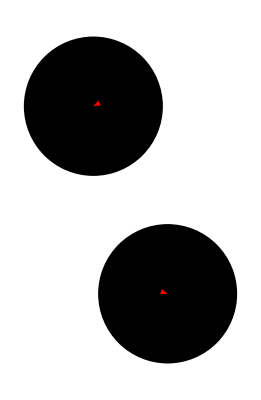

```mathematica
particles[0]=Graphics[Table[Disk[{X[0][i],Y[0][i]},a],{i,1,NMAX}]];
forces[0]=Graphics[{Red,Table[Arrow[{{X[0][i],Y[0][i]},{X[0][i]+Re[FX[0][i]],Y[0][i]+Re[FY[0][i]]}}],{i,1,NMAX}]}];
frame[0]=Show[{particles[0],forces[0]}]
```

# Evolution

```mathematica
ω
```

3.14016×10^9

```mathematica
dt=1
```

1

```mathematica
γ
```

551.724

```mathematica
MAXstep=200;
```

```mathematica
For[step=1,step<MAXstep,step++,
Table[{vX[step][n]=vX[step-1][n] ⅇ^(-γ dt)+Chop[FX[step-1][n]]dt/mass,vY[step][n]=vY[step-1][n] ⅇ^(-γ dt)+Chop[FY[step-1][n]]dt/mass,vZ[step][n]=0},{n,1,NMAX}];
Table[{X[step][n]=X[step-1][n]+Chop[vX[step][n]]dt,Y[step][n]=Y[step-1][n]+Chop[vY[step][n]]dt,Z[step][n]=0},{n,1,NMAX}];
particles[step]=Graphics[Table[Disk[{X[step][i],Y[step][i]},a],{i,1,NMAX}]];
forces[step]=Graphics[{Red,Table[Arrow[{{X[step][i],Y[step][i]},{X[step][i]+Re[FX[step][i]],Y[step][i]+Re[FY[step][i]]}}],{i,1,NMAX}]}];
frame[step]=Show[{particles[step],forces[step]}];
PP[step]=(1/αα)(Inverse[nZ[step]].Einc[step]);
cPP[step]=(1/cαα)Inverse[cnZ[step]].cEinc[step];
Table[Evaluate[PPP[step][[i]]]=PP[step][[i]],{i,1,3NMAX}];
Table[Evaluate[cPPP[step][[i]]]=cPP[step][[i]],{i,1,3NMAX}];
]
```

General::munfl: Exp[-19955.3] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

```mathematica
forces[5]
```

-Graphics-

```mathematica
X[0][2]
X[1][2]
```

17.5925

16.9514

```mathematica
Animate[Show[{particles[step],forces[step]},PlotRange->{{-1λ,1λ},{-1λ,1λ}}],{step,0,MAXstep-1,1}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Google Drive\KU\Research at KU\Optical Binding

```mathematica
animation=Table[Show[{particles[step],forces[step]},PlotRange->{{-1λ,1λ},{-1λ,1λ}}],{step,0,MAXstep-1,1}];
```

```mathematica
Export["5plane.gif",animation]
```

ToExpression::esntx: Could not parse 12.1 as input.

5plane.gif

```mathematica
positions=Table[{X[step-1][n],Y[step-1][n]},{n,1,NMAX},{step,0,MAXstep-1,1}];
```

```mathematica
Export["positions1.csv",positions]
```

positions1.csv

```mathematica
velocities=Table[{vX[step-1][n],vY[step-1][n]},{n,1,NMAX},{step,0,MAXstep-1,1}];
```

```mathematica
Export["velocities1.csv",velocities]
```

velocities1.csv

```mathematica
force=Table[{Re[FX[step-1][n]],Re[FY[step-1][n]]},{n,1,NMAX},{step,1,100}];
```

General::munfl: Exp[-19955.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-189817.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
force
```

{{{-1.285×10^-9,-1.03375×10^-11},{-1.30276×10^-9,-6.65942×10^-12},{-1.3209×10^-9,-2.94163×10^-12},{-1.33946×10^-9,8.15297×10^-13},{-1.35845×10^-9,4.61072×10^-12},{-1.37787×10^-9,8.44388×10^-12},{-1.39775×10^-9,1.23138×10^-11},{-1.4181×10^-9,1.62196×10^-11},{-1.43895×10^-9,2.01598×10^-11},{-1.4603×10^-9,2.41331×10^-11},{-1.48218×10^-9,2.81378×10^-11},{-1.5046×10^-9,3.21721×10^-11},{-1.5276×10^-9,3.62338×10^-11},{-1.55118×10^-9,4.03205×10^-11},{-1.57539×10^-9,4.44295×10^-11},{-1.60023×10^-9,4.85576×10^-11},{-1.62575×10^-9,5.27014×10^-11},{-1.65196×10^-9,5.68571×10^-11},{-1.6789×10^-9,6.10201×10^-11},{-1.7066×10^-9,6.51856×10^-11},{-1.7351×10^-9,6.93481×10^-11},{-1.76443×10^-9,7.35014×10^-11},{-1.79464×10^-9,7.76387×10^-11},{-1.82576×10^-9,8.17522×10^-11},{-1.85784×10^-9,8.58332×10^-11},{-1.89093×10^-9,8.98723×10^-11},{-1.92509×10^-9,9.38585×10^-11},{-1.96037×10^-9,9.77798×10^-11},{-1.99683×10^-9,1.01623×10^-10},{-2.03337×10^-9,1.05642×10^-10},{-2.07113×10^-9,1.09565×10^-10},{-2.11018×10^-9,1.13375×10^-10},{-2.15059×10^-9,1.17049×10^-10},{-2.19246×10^-9,1.20565×10^-10},{-2.23589×10^-9,1.23895×10^-10},{-2.28096×10^-9,1.27011×10^-10},{-2.32781×10^-9,1.29879×10^-10},{-2.37657×10^-9,1.32462×10^-10},{-2.42737×10^-9,1.34717×10^-10},{-2.48037×10^-9,1.36596×10^-10},{-2.53576×10^-9,1.38046×10^-10},{-2.59374×10^-9,1.39006×10^-10},{-2.65452×10^-9,1.39405×10^-10},{-2.71838×10^-9,1.39164×10^-10},{-2.78561×10^-9,1.38193×10^-10},{-2.85652×10^-9,1.36388×10^-10},{-2.93151×10^-9,1.33628×10^-10},{-3.01102×10^-9,1.29776×10^-10},{-3.09554×10^-9,1.24671×10^-10},{-3.18567×10^-9,1.18127×10^-10},{-3.28211×10^-9,1.09928×10^-10},{-3.38564×10^-9,9.98174×10^-11},{-3.49934×10^-9,8.78878×10^-11},{-3.62216×10^-9,7.33732×10^-11},{-3.75538×10^-9,5.58256×10^-11},{-3.90056×10^-9,3.47035×10^-11},{-4.05957×10^-9,9.3489×10^-12},{-4.23471×10^-9,-2.10442×10^-11},{-4.4288×10^-9,-5.74703×10^-11},{-4.64537×10^-9,-1.01168×10^-10},{-4.89182×10^-9,-1.52468×10^-10},{-5.17282×10^-9,-2.1369×10^-10},{-5.49643×10^-9,-2.86966×10^-10},{-5.87332×10^-9,-3.75002×10^-10},{-6.3179×10^-9,-4.81267×10^-10},{-6.85005×10^-9,-6.1026×10^-10},{-7.49789×10^-9,-7.67895×10^-10},{-8.30249×10^-9,-9.62075×10^-10},{-9.32598×10^-9,-1.20355×10^-9},{-1.06667×10^-8,-1.50728×10^-9},{-1.24895×10^-8,-1.8947×10^-9},{-1.50906×10^-8,-2.39759×10^-9},{-1.90569×10^-8,-3.06522×10^-9},{-2.43196×10^-8,-3.97612×10^-9},{0.00113432,7.45826×10^-7},{-1.55547×10^-28,2.4442×10^-26},{-1.55596×10^-28,2.45198×10^-26},{-1.55646×10^-28,2.45975×10^-26},{-1.55695×10^-28,2.46752×10^-26},{-1.55744×10^-28,2.47528×10^-26},{-1.55794×10^-28,2.48304×10^-26},{-1.55844×10^-28,2.4908×10^-26},{-1.55894×10^-28,2.49854×10^-26},{-1.55944×10^-28,2.50629×10^-26},{-1.55994×10^-28,2.51402×10^-26},{-1.56044×10^-28,2.52176×10^-26},{-1.56094×10^-28,2.52948×10^-26},{-1.56145×10^-28,2.5372×10^-26},{-1.56195×10^-28,2.54492×10^-26},{-1.56246×10^-28,2.55263×10^-26},{-1.56297×10^-28,2.56033×10^-26},{-1.56347×10^-28,2.56803×10^-26},{-1.56398×10^-28,2.57573×10^-26},{-1.5645×10^-28,2.58342×10^-26},{-1.56501×10^-28,2.5911×10^-26},{-1.56552×10^-28,2.59878×10^-26},{-1.56604×10^-28,2.60645×10^-26},{-1.56655×10^-28,2.61412×10^-26},{-1.56707×10^-28,2.62178×10^-26},{-1.56759×10^-28,2.62944×10^-26}},{{-3.85936×10^-10,-2.05086×10^-9},{-3.91816×10^-10,-2.08109×10^-9},{-3.97901×10^-10,-2.11195×10^-9},{-4.04199×10^-10,-2.14344×10^-9},{-4.10717×10^-10,-2.17559×10^-9},{-4.17463×10^-10,-2.20842×10^-9},{-4.24446×10^-10,-2.24193×10^-9},{-4.31674×10^-10,-2.27615×10^-9},{-4.39157×10^-10,-2.3111×10^-9},{-4.46905×10^-10,-2.34678×10^-9},{-4.54927×10^-10,-2.38322×10^-9},{-4.63233×10^-10,-2.42044×10^-9},{-4.71834×10^-10,-2.45845×10^-9},{-4.80741×10^-10,-2.49728×10^-9},{-4.89965×10^-10,-2.53694×10^-9},{-4.99518×10^-10,-2.57745×10^-9},{-5.09412×10^-10,-2.61882×10^-9},{-5.1966×10^-10,-2.66109×10^-9},{-5.30274×10^-10,-2.70427×10^-9},{-5.41268×10^-10,-2.74837×10^-9},{-5.52656×10^-10,-2.79342×10^-9},{-5.64452×10^-10,-2.83944×10^-9},{-5.7667×10^-10,-2.88645×10^-9},{-5.89325×10^-10,-2.93446×10^-9},{-6.02433×10^-10,-2.98349×10^-9},{-6.16009×10^-10,-3.03357×10^-9},{-6.30068×10^-10,-3.0847×10^-9},{-6.44628×10^-10,-3.13691×10^-9},{-6.59703×10^-10,-3.19022×10^-9},{-6.75797×10^-10,-3.24546×10^-9},{-6.92486×10^-10,-3.30188×10^-9},{-7.0979×10^-10,-3.3595×10^-9},{-7.2773×10^-10,-3.41831×10^-9},{-7.46323×10^-10,-3.47834×10^-9},{-7.65589×10^-10,-3.53957×10^-9},{-7.85547×10^-10,-3.60203×10^-9},{-8.06213×10^-10,-3.6657×10^-9},{-8.27603×10^-10,-3.73058×10^-9},{-8.49734×10^-10,-3.79665×10^-9},{-8.72618×10^-10,-3.86391×10^-9},{-8.96265×10^-10,-3.93231×10^-9},{-9.20683×10^-10,-4.00183×10^-9},{-9.45876×10^-10,-4.07242×10^-9},{-9.71843×10^-10,-4.14403×10^-9},{-9.98578×10^-10,-4.21657×10^-9},{-1.02607×10^-9,-4.28997×10^-9},{-1.05429×10^-9,-4.36412×10^-9},{-1.0832×10^-9,-4.43887×10^-9},{-1.11278×10^-9,-4.51408×10^-9},{-1.14294×10^-9,-4.58956×10^-9},{-1.17362×10^-9,-4.66506×10^-9},{-1.2047×10^-9,-4.74032×10^-9},{-1.2351×10^-9,-4.81416×10^-9},{-1.26565×10^-9,-4.88707×10^-9},{-1.2962×10^-9,-4.9586×10^-9},{-1.32652×10^-9,-5.02819×10^-9},{-1.35634×10^-9,-5.09516×10^-9},{-1.38535×10^-9,-5.15871×10^-9},{-1.41313×10^-9,-5.21782×10^-9},{-1.43918×10^-9,-5.27129×10^-9},{-1.46152×10^-9,-5.31685×10^-9},{-1.47988×10^-9,-5.35297×10^-9},{-1.49305×10^-9,-5.37726×10^-9},{-1.49948×10^-9,-5.38671×10^-9},{-1.49723×10^-9,-5.37754×10^-9},{-1.48381×10^-9,-5.34493×10^-9},{-1.45607×10^-9,-5.28273×10^-9},{-1.40996×10^-9,-5.18298×10^-9},{-1.3403×10^-9,-5.03525×10^-9},{-1.2405×10^-9,-4.82576×10^-9},{-1.10234×10^-9,-4.53603×10^-9},{-9.16226×10^-10,-4.14095×10^-9},{-6.73229×10^-10,-3.60598×10^-9},{-3.73937×10^-10,-2.88434×10^-9},{-3.55524×10^-11,-1.98805×10^-9},{-5.86701×10^-12,-5.68793×10^-10},{-5.86701×10^-12,-5.68398×10^-10},{-5.86701×10^-12,-5.68003×10^-10},{-5.86701×10^-12,-5.67608×10^-10},{-5.86701×10^-12,-5.67214×10^-10},{-5.86701×10^-12,-5.6682×10^-10},{-5.86701×10^-12,-5.66426×10^-10},{-5.86701×10^-12,-5.66033×10^-10},{-5.86701×10^-12,-5.65639×10^-10},{-5.86701×10^-12,-5.65246×10^-10},{-5.86702×10^-12,-5.64854×10^-10},{-5.86702×10^-12,-5.64461×10^-10},{-5.86702×10^-12,-5.64069×10^-10},{-5.86702×10^-12,-5.63677×10^-10},{-5.86702×10^-12,-5.63285×10^-10},{-5.86702×10^-12,-5.62894×10^-10},{-5.86702×10^-12,-5.62503×10^-10},{-5.86702×10^-12,-5.62112×10^-10},{-5.86702×10^-12,-5.61722×10^-10},{-5.86702×10^-12,-5.61331×10^-10},{-5.86702×10^-12,-5.60941×10^-10},{-5.86702×10^-12,-5.60552×10^-10},{-5.86702×10^-12,-5.60162×10^-10},{-5.86702×10^-12,-5.59773×10^-10},{-5.86702×10^-12,-5.59384×10^-10}},{{2.01605×10^-9,1.01208×10^-9},{2.04174×10^-9,1.04119×10^-9},{2.06807×10^-9,1.07096×10^-9},{2.09507×10^-9,1.10142×10^-9},{2.12277×10^-9,1.13257×10^-9},{2.15118×10^-9,1.16445×10^-9},{2.18034×10^-9,1.19706×10^-9},{2.21027×10^-9,1.23044×10^-9},{2.241×10^-9,1.26461×10^-9},{2.27257×10^-9,1.29958×10^-9},{2.305×10^-9,1.33539×10^-9},{2.33833×10^-9,1.37205×10^-9},{2.3726×10^-9,1.4096×10^-9},{2.40783×10^-9,1.44806×10^-9},{2.44408×10^-9,1.48746×10^-9},{2.48138×10^-9,1.52783×10^-9},{2.51978×10^-9,1.56919×10^-9},{2.55933×10^-9,1.61157×10^-9},{2.60006×10^-9,1.65502×10^-9},{2.64205×10^-9,1.69955×10^-9},{2.68533×10^-9,1.74521×10^-9},{2.72997×10^-9,1.79203×10^-9},{2.77603×10^-9,1.84004×10^-9},{2.82358×10^-9,1.88929×10^-9},{2.87268×10^-9,1.9398×10^-9},{2.92342×10^-9,1.99162×10^-9},{2.97587×10^-9,2.04479×10^-9},{3.03011×10^-9,2.09935×10^-9},{3.08624×10^-9,2.15534×10^-9},{3.14378×10^-9,2.21348×10^-9},{3.20336×10^-9,2.27319×10^-9},{3.26509×10^-9,2.33453×10^-9},{3.32909×10^-9,2.39755×10^-9},{3.39548×10^-9,2.4623×10^-9},{3.4644×10^-9,2.52884×10^-9},{3.53601×10^-9,2.59723×10^-9},{3.61046×10^-9,2.66751×10^-9},{3.68793×10^-9,2.73975×10^-9},{3.76861×10^-9,2.81401×10^-9},{3.85273×10^-9,2.89035×10^-9},{3.94051×10^-9,2.96883×10^-9},{4.0322×10^-9,3.04952×10^-9},{4.1281×10^-9,3.13248×10^-9},{4.22852×10^-9,3.21777×10^-9},{4.33381×10^-9,3.30546×10^-9},{4.44436×10^-9,3.39561×10^-9},{4.56063×10^-9,3.48829×10^-9},{4.68311×10^-9,3.58356×10^-9},{4.81237×10^-9,3.68148×10^-9},{4.94906×10^-9,3.78211×10^-9},{5.09394×10^-9,3.8855×10^-9},{5.24786×10^-9,3.99169×10^-9},{5.41274×10^-9,4.09934×10^-9},{5.58883×10^-9,4.20991×10^-9},{5.77749×10^-9,4.32346×10^-9},{5.98037×10^-9,4.44003×10^-9},{6.19941×10^-9,4.55965×10^-9},{6.43699×10^-9,4.68231×10^-9},{6.69601×10^-9,4.808×10^-9},{6.98009×10^-9,4.93666×10^-9},{7.29493×10^-9,5.06594×10^-9},{7.64595×10^-9,5.19638×10^-9},{8.04096×10^-9,5.32712×10^-9},{8.49033×10^-9,5.4569×10^-9},{9.00807×10^-9,5.58389×10^-9},{9.61368×10^-9,5.70542×10^-9},{1.0335×10^-8,5.81752×10^-9},{1.12131×10^-8,5.91419×10^-9},{1.23113×10^-8,5.98614×10^-9},{1.37318×10^-8,6.01847×10^-9},{1.56508×10^-8,5.98627×10^-9},{1.83971×10^-8,5.84501×10^-9},{2.2657×10^-8,5.50732×10^-9},{2.87202×10^-8,4.77249×10^-9},{-0.00113431,-7.47885×10^-7},{5.67427×10^-28,-1.80414×10^-25},{5.67065×10^-28,-1.80337×10^-25},{5.66704×10^-28,-1.80259×10^-25},{5.66343×10^-28,-1.80181×10^-25},{5.65983×10^-28,-1.80104×10^-25},{5.65623×10^-28,-1.80026×10^-25},{5.65263×10^-28,-1.79949×10^-25},{5.64904×10^-28,-1.79871×10^-25},{5.64545×10^-28,-1.79794×10^-25},{5.64186×10^-28,-1.79716×10^-25},{5.63828×10^-28,-1.79639×10^-25},{5.63471×10^-28,-1.79562×10^-25},{5.63114×10^-28,-1.79485×10^-25},{5.62757×10^-28,-1.79408×10^-25},{5.624×10^-28,-1.79331×10^-25},{5.62044×10^-28,-1.79254×10^-25},{5.61689×10^-28,-1.79177×10^-25},{5.61334×10^-28,-1.791×10^-25},{5.60979×10^-28,-1.79023×10^-25},{5.60624×10^-28,-1.78946×10^-25},{5.6027×10^-28,-1.7887×10^-25},{5.59917×10^-28,-1.78793×10^-25},{5.59564×10^-28,-1.78716×10^-25},{5.59211×10^-28,-1.7864×10^-25},{5.58858×10^-28,-1.78563×10^-25}}}

```mathematica
Export["forces.csv",force]
```

forces.csv

```mathematica
dip[st_][i_]:=PPP[st][[i;;i+2]]
cdip[st_][i_]:=cPPP[st][[i;;i+2]]
absdip[st_][i_]:=Chop[√(PPP[st][[i;;i+2]].cPPP[st][[i;;i+2]])]
```

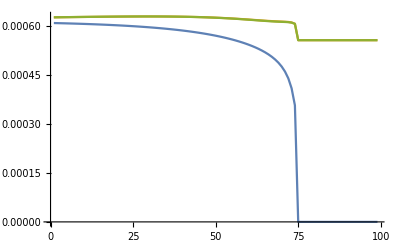

```mathematica
ListPlot[{Table[absdip[st][1],{st,1,MAXstep-1}],Table[absdip[st][2],{st,1,MAXstep-1}],Table[absdip[st][3],{st,1,MAXstep-1}]},PlotRange->All,Joined->True]
```

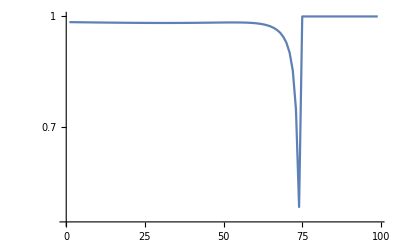

```mathematica
ListLogPlot[Table[Abs[Det[nZ[st]]],{st,1,MAXstep-1}],PlotRange->All,Joined->True]
```

# References

### references

-Graphics-

-Graphics-

-Graphics-

```mathematica
α0=4π ϵ0 a^3(ϵ-1)/(ϵ+2);
```

```mathematica
α=α0/(1-(ⅈ α0 k0^3)/(6π ϵ0));
```

```mathematica
αr=ComplexExpand[Re[α]]//FullSimplify
αi=ComplexExpand[Im[α]]//FullSimplify
```

(36 a^3 π (-1+ϵ) (2+ϵ) ϵ0)/(4 a^6 k0^6 (-1+ϵ)^2+9 (2+ϵ)^2)

(24 a^6 k0^3 π (-1+ϵ)^2 ϵ0)/(4 a^6 k0^6 (-1+ϵ)^2+9 (2+ϵ)^2)

```mathematica
c=1/(√(ϵ0 μ0));
```

```mathematica
η0=√(μ0/ϵ0);
```

```mathematica
k0=(2π)/λ;
```

```mathematica
σ=k0 αi/ϵ0
```

(384 a^6 π^5 (-1+ϵ)^2)/((9 (2+ϵ)^2+(256 a^6 π^6 (-1+ϵ)^2)/λ^6) λ^4)

```mathematica
H0=E0/η0;
```

```mathematica
FRP=Simplify[1/2 σ/c E0 H0,{ϵ0>0,μ0>0,λ>0,a>0}]
```

(192 a^6 E0^2 π^5 (-1+ϵ)^2 ϵ0 λ^2)/(256 a^6 π^6 (-1+ϵ)^2+9 (2+ϵ)^2 λ^6)

```mathematica
GF=Simplify[1/4 αr E0^2/λ,{ϵ0>0,μ0>0,λ>0,a>0}]
```

(9 a^3 E0^2 π (-1+ϵ) (2+ϵ) ϵ0 λ^5)/(256 a^6 π^6 (-1+ϵ)^2+9 (2+ϵ)^2 λ^6)

```mathematica
FRP/GF/.ϵ->4/.a->λ/10.
```

1.03903

### force

```mathematica
(1.33^2+ⅈ 0.2-1)/(1.33^2+ⅈ 0.2+2)
```

0.206247+0.0421212 ⅈ

```mathematica
1.33^2
```

1.7689